# Parameters & Configuration

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
Omm=0.3111;
Oml=1-Omm;
H0=1/2997.9;
Lp4=4;
```

```mathematica
h=0.6766
```

0.6766

## Data imput

## Covariance Integrals

```mathematica
zsigma=Import["sigma8_CAMB.dat","Table"];
```

```mathematica
varcosmicMONObare=Import["integrals/varcosmic_mono_bare.dat","Table"];
varcosmicDIPbare=Import["integrals/varcosmic_dip_bare.dat","Table"];
varcosmicQUADbare=Import["integrals/varcosmic_quad_bare.dat","Table"];
varcosmicOCTbare=Import["integrals/varcosmic_oct_bare.dat","Table"];
varcosmicHEXAbare=Import["integrals/varcosmic_hexa_bare.dat","Table"];
varcosmic02bare=Import["integrals/varcosmic_mult02_bare.dat","Table"];
varcosmic04bare=Import["integrals/varcosmic_mult04_bare.dat","Table"];
varcosmic13bare=Import["integrals/varcosmic_mult13_bare.dat","Table"];
varcosmic24bare=Import["integrals/varcosmic_mult24_bare.dat","Table"];
varmixMONObare=Import["integrals/varmix_mono_bare.dat","Table"];
varmixDIPbare=Import["integrals/varmix_dip_bare.dat","Table"];
varmixQUADbare=Import["integrals/varmix_quad_bare.dat","Table"];
varmixOCTbare=Import["integrals/varmix_oct_bare.dat","Table"];
varmixHEXAbare=Import["integrals/varmix_hexa_bare.dat","Table"];
varmix02bare=Import["integrals/varmix_mult02_bare.dat","Table"];
varmix04bare=Import["integrals/varmix_mult04_bare.dat","Table"];
varmix13bare=Import["integrals/varmix_mult13_bare.dat","Table"];
varmix24bare=Import["integrals/varmix_mult24_bare.dat","Table"];
```

## Signals Integrals

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu1_z0_fid.dat","Table"];
```

```mathematica
nu1=Interpolation[nu1baretab];
```

```mathematica
nu1z0[d_]:=d H0 nu1[d];
```

MONOPOLE

```mathematica
mu0baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu0_z0_fid.dat","Table"];
```

```mathematica
mu0=Interpolation[mu0baretab];
```

```mathematica
mu0z0[d_]:= mu0[d];
```

QUADRUPOLE

```mathematica
mu2baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu2_z0_fid.dat","Table"];
```

```mathematica
mu2=Interpolation[mu2baretab];
```

```mathematica
mu2z0[d_]:=mu2[d];
```

OCTUPOLE

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu3_z0_fid.dat","Table"];
```

```mathematica
nu3=Interpolation[nu1baretab];
```

```mathematica
nu3z0[d_]:=d H0 nu3[d];
```

HEXADECAPOLE

```mathematica
mu4baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu4_z0_fid.dat","Table"];
mu4=Interpolation[mu4baretab];
mu4z0[d_]:= mu4[d];
```

```mathematica
mu0Lp4zbaretab=Table[mu0z0[d],{d,4,172,4}];
nu1Lp4zbaretab=Table[nu1z0[d],{d,4,172,4}];
mu2Lp4zbaretab=Table[mu2z0[d],{d,4,172,4}];
nu3Lp4zbaretab=Table[nu3z0[d],{d,4,172,4}];
mu4Lp4zbaretab=Table[mu4z0[d],{d,4,172,4}];
```

## Cosmology

```mathematica
r[z_]:=Integrate[1/(Sqrt[Omm x^3+Oml]),{x,1,1+z}];
```

```mathematica
r[0.15]/H0
```

433.566

```mathematica
D1[z_]:=5Omm/2(Omm(1+z)^3+1-Omm)^(1/2)NIntegrate[1/(Omm/x+(1-Omm) x^2)^(3/2),{x,0,1/(1+z)}]
```

```mathematica
fz[z_]:=1/(Omm+Oml/(1+z)^3)(-3Omm/2+5Omm/2/(1+z)/D1[z]);
```

```mathematica
HH[z_]=Sqrt[Omm(1+z)+(1-Omm)/(1+z)^2];
```

```mathematica
dD1dz[z_]:=(5 Omm /2) (3 Omm (1+z)^2/(2 Sqrt[Omm (1+z)^3 + Oml]) Integrate[(1+x)/(Sqrt[Omm(1+x)^3+Oml])^3,{x,z,Infinity}] - (1+z)/(Omm(1+z)^3+Oml))
```

```mathematica
Table[{D1[0],fz[0]},{i,1}]
```

{{0.785555,0.523414}}

```mathematica
OmegaLz[z_]:=1/(Omm (1+z)^3+Oml)
```

```mathematica
OmegaMz[z_]:= Omm (1+z)^3/(Omm(1+z)^3+Oml)
```

```mathematica
zSKA=List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95]; 
(* zSKA= List[0.20,0.28,0.36,0.44,0.53,0.64,0.79, 1.03, 1.31, 1.58, 1.86]; *)
```

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
VzSKA=ParallelTable[4/3 Pi ( r[zSKA[[i]]+0.05]^3-r[zSKA[[i]]-0.05]^3)/H0^3 30000/41253,{i,1,ktot}];
fzSKA=ParallelTable[fz[zSKA[[i]]],{i,1,ktot}];
evolzSKA=ParallelTable[(D1[zSKA[[i]]]/D1[0])^2,{i,1,ktot}];
dzSKA=ParallelTable[r[zSKA[[i]]],{i,1,ktot}];
HzSKA=ParallelTable[HH[zSKA[[i]]],{i,1,ktot}];
dD1dzSKA=ParallelTable[dD1dz[zSKA[[i]]],{i,1,ktot}];
D1zSKA=Table[D1[i],{i,zSKA}];
D10=D1[0];
dfdzSKA=(3 Oml (1+zSKA)^2)/(Omm (1+zSKA)^3+Oml)^2 (-3 Omm/2 + 5 Omm /2 /((1+zSKA) D1zSKA)) - (5 Omm /2 )((1+zSKA)^3/(Omm(1+zSKA)^3+Oml))((D1zSKA+(1+zSKA) dD1dzSKA)/((1+zSKA)D1zSKA)^2);
rH0zSKA = r[zSKA];
```

```mathematica
VzSKA
```

{4.90045×10^8,1.20103×10^9,2.09836×10^9,3.09231×10^9,4.11482×10^9,5.11741×10^9,6.06784×10^9,6.94656×10^9,7.74333×10^9,8.45454×10^9,9.08098×10^9,9.62628×10^9,1.00957×10^10,1.04954×10^10,1.08317×10^10,1.11109×10^10,1.13393×10^10,1.15223×10^10,1.16654×10^10}

```mathematica
D1zSKA
```

{0.725792,0.688431,0.653295,0.620452,0.589882,0.561505,0.535207,0.510852,0.488297,0.467398,0.448017,0.430022,0.413292,0.397715,0.383189,0.369621,0.356928,0.345034,0.333872}

```mathematica
OmegaMzSKA=OmegaMz[zSKA]
```

{0.407165,0.468653,0.526309,0.579253,0.627097,0.669814,0.707623,0.740885,0.770035,0.795522,0.817786,0.837237,0.854242,0.869129,0.882186,0.893661,0.903769,0.912694,0.920593}

```mathematica
OmegaLzSKA=OmegaLz[zSKA]
```

{0.860552,0.771297,0.687605,0.610751,0.541302,0.479294,0.424412,0.376128,0.333815,0.296818,0.264499,0.236266,0.211581,0.18997,0.171017,0.15436,0.139688,0.126733,0.115266}

```mathematica
dOmegaLzSKA=- 3 Omm (1+zSKA)^2/(Omm(1+zSKA)^3+Oml)^2
```

{-0.914054,-0.86753,-0.804206,-0.731958,-0.656998,-0.583706,-0.51484,-0.451894,-0.395461,-0.345549,-0.301819,-0.263747,-0.230734,-0.202174,-0.177493,-0.156165,-0.137723,-0.121756,-0.107912}

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
bBzSKA=bmeanzSKA+dbz/2;
bFzSKA=bmeanzSKA-dbz/2;
bTzSKA=(bBzSKA+bFzSKA)/2;
```

```mathematica
bBzSKA
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bB0=b1+db/2
bF0=b1-db/2
```

1.054

0.054

```mathematica
b1B=b1;
b1F=b1;
b2B=b2;
b2F=b2;
```

```mathematica
b1B
```

0.554

Import CAMB results

```mathematica
Length[zsigma]
```

100

Redshift is displayed in the wrong order in zsigma. σ8 is given i

```mathematica
sigma8ztab=zsigma[[All,2]];
```

```mathematica
redshifts=zsigma[[All,1]];
```

```mathematica
zsigma8tab=Table[{redshifts[[i]],sigma8ztab[[i]]},{i,1,Length[redshifts]}];
```

```mathematica
sigma8z=Interpolation[zsigma8tab];
```

```mathematica
Sigma8z0=sigma8z[0]
```

0.814468

```mathematica
sigma8z[0]*D1[0.5]/D1[0]
```

0.627151

```mathematica
sigma8z[0.5]
```

0.627168

```mathematica
Sigma8zSKA=sigma8z[zSKA];
```

Need of fevolB and fevolF

```mathematica
bBtildezSKA=bBzSKA D1zSKA Sigma8z0/D10
bFtildezSKA=bFzSKA D1zSKA Sigma8z0/D10
```

{0.845096,0.837813,0.832225,0.828564,0.826993,0.827618,0.830509,0.835711,0.843256,0.853172,0.865485,0.880225,0.897432,0.917153,0.939447,0.964384,0.992045,1.02253,1.05594}

{0.0925901,0.124044,0.154884,0.185276,0.2154,0.245446,0.275603,0.306056,0.336987,0.368571,0.400978,0.434376,0.468928,0.5048,0.542155,0.581158,0.62198,0.664792,0.709776}

```mathematica
bBtildezSKA-bFtildezSKA
```

{0.752505,0.713769,0.677341,0.643289,0.611593,0.582172,0.554906,0.529655,0.50627,0.484602,0.464507,0.44585,0.428504,0.412353,0.397292,0.383225,0.370065,0.357734,0.346161}

```mathematica
(bBtildezSKA+bFtildezSKA)/2
```

{0.468843,0.480929,0.493555,0.50692,0.521196,0.536532,0.553056,0.570883,0.590122,0.610871,0.633231,0.6573,0.68318,0.710977,0.740801,0.772771,0.807012,0.843659,0.882856}

# Multi-SPLIT Covariance

## Covariance Blocks

## Parameters

### Galaxy bias

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_, dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_, dbz_]:=bmeanzSKA-dbz/m;
bT[m_,dbz_]:=bmeanzSKA ;
```

#### Standard splitting 50% (m = 2)

```mathematica
m = 2;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA50=bB[2, dbz]
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA50=bF[2,dbz]
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bTzSKA50 = bT[2,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

BRIGHT

```mathematica
nBSKA50 = 1/2;
```

```mathematica
smodelBzSKA50 = List[0.22441708,0.35788955,0.47077869,0.54038551,0.60761985,0.67991981,0.7531311,0.81864417,0.88081715,0.94857743,1.02785004,1.12008456,1.21930805,1.32187692,1.42534363,1.52897325,1.63180455,1.73334715,1.83420913];
```

```mathematica
fevolBzSKA50 = List[3.00956639,0.07976877,-0.81552783,-0.6173486,-0.39242556,-0.31155665,-0.26595514,-0.1091582,0.07791229,0.18253319,0.17336397,0.03980399,-0.12308668,-0.28681099,-0.41997146,-0.51728093,-0.57341237,-0.57764042,-0.55234844];
```

FAINT

```mathematica
nFSKA50 = 1/2;
```

```mathematica
smodelzSKA50 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=2,m=1/(1-nFSKA50);]
```

```mathematica
m
```

2

```mathematica
smodelFzSKA50 = (m/(m-1)) smodelzSKA50 -(1/(m-1)) smodelBzSKA50
```

{-0.0218816,-0.0219979,0.021057,0.140457,0.279574,0.415079,0.541364,0.669872,0.797998,0.918387,1.02899,1.12851,1.22639,1.32445,1.42711,1.53507,1.64911,1.77015,1.89163}

```mathematica
fevolFzSKA50 = List[1.49669846,4.74321837,4.48561914,3.00325909,1.42466759,0.23953114,-0.63019961,-1.38888192,-2.01572455,-2.47043394,-2.7319998,-2.83059041,-2.87381247,-2.89939059,-2.94565432,-3.01777315,-3.12068025,-3.25274921,-3.36209773];
```

#### Splitting with 70% Bright (m=10/7)

```mathematica
m=10/7;
```

```mathematica
db=0.8;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA30=bB[10/3, dbz]
```

{1.18304,1.23379,1.28867,1.34801,1.41219,1.4816,1.55666,1.63784,1.72563,1.82056,1.92323,2.03426,2.15434,2.28419,2.42462,2.57649,2.74073,2.91834,3.11042}

```mathematica
bFzSKA30=bF[10/3,dbz]
```

{0.383042,0.433787,0.488665,0.548013,0.612194,0.681603,0.756665,0.83784,0.925627,1.02056,1.12323,1.23426,1.35434,1.48419,1.62462,1.77649,1.94073,2.11834,2.31042}

```mathematica
bTzSKA30 = bT[10/3,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

BRIGHT

```mathematica
nBSKA30 = 7/10;
```

```mathematica
smodelBzSKA30 = List[0.23092495,0.33891824,0.42179897,0.49729887,0.55974349,0.60437846,0.65341957,0.72717735,0.82383668,0.92773427,1.03454971,1.14181863,1.24827165,1.35407972,1.45894099,1.56296605,1.6661472,1.7681241,1.86971955];
```

```mathematica
fevolBzSKA30 = List[2.30477429,-1.04874158,-0.67796927,-0.66294643,-0.34399838,0.11218844,0.42949383,0.37159525,0.06233465,-0.28992148,-0.60506652,-0.87795657,-1.08670387,-1.2532168,-1.37215364,-1.44791514,-1.48462593,-1.47256817,-1.4354558];
```

FAINT

```mathematica
nFSKA30 = 3/10;
```

```mathematica
smodelzSKA30 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=3,m=1/(1-nFSKA30);]
m
```

10/7

```mathematica
smodelFzSKA30 = (m/(m-1)) smodelzSKA30 -(1/(m-1)) smodelBzSKA30
```

{-0.201266,-0.23099,-0.164471,-0.0256268,0.172588,0.414782,0.632845,0.784113,0.875739,0.946894,1.01411,1.08342,1.16353,1.25102,1.3499,1.45982,1.58052,1.71353,1.84704}

```mathematica
fevolFzSKA30 = List[2.13263474,10.48537558,7.69874714,5.52339249,2.52306627,-0.38181554,-2.49574352,-3.36378913,-3.37513461,-3.13668448,-2.85257116,-2.60274536,-2.45918956,-2.38616343,-2.40768448,-2.51328814,-2.69269385,-2.94799033,-3.17468009];
```

### Survey

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.200168},{0.25,0.117195},{0.35,0.0697361},{0.45,0.0422937},{0.55,0.0260542},{0.65,0.0164978},{0.75,0.0105573},{0.85,0.00681219},{0.95,0.00439079},{1.05,0.00280882},{1.15,0.00179506},{1.25,0.00113967},{1.35,0.000716732},{1.45,0.000448765},{1.55,0.000276039},{1.65,0.000167883},{1.75,0.00010073},{1.85,0.000059082},{1.95,0.0000338995}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.200168,0.117195,0.0697361,0.0422937,0.0260542,0.0164978,0.0105573,0.00681219,0.00439079,0.00280882,0.00179506,0.00113967,0.000716732,0.000448765,0.000276039,0.000167883,0.00010073,0.000059082,0.0000338995}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.23016×10^8

```mathematica
nBzSKA50=Table[nBSKA50, {i,Length[zSKA]}];
nFzSKA50=Table[nFSKA50, {i,Length[zSKA]}];
nBzSKA30=Table[nBSKA30, {i,Length[zSKA]}];
nFzSKA30=Table[nFSKA30, {i,Length[zSKA]}];
```

```mathematica
nBzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nFzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nBzSKA30
```

{7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10,7/10}

```mathematica
nFzSKA30
```

{3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10,3/10}

```mathematica
NbarBzSKA50=NbarzSKA*nBzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarFzSKA50=NbarzSKA*nFzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarBzSKA30=NbarzSKA*nBzSKA30
```

{0.140118,0.0820368,0.0488153,0.0296056,0.0182379,0.0115484,0.00739009,0.00476853,0.00307355,0.00196617,0.00125654,0.000797768,0.000501713,0.000314135,0.000193227,0.000117518,0.000070511,0.0000413574,0.0000237297}

```mathematica
NbarFzSKA30=NbarzSKA*nFzSKA30
```

{0.0600505,0.0351586,0.0209208,0.0126881,0.00781626,0.00494933,0.00316718,0.00204366,0.00131724,0.000842645,0.000538518,0.000341901,0.00021502,0.000134629,0.0000828116,0.000050365,0.000030219,0.0000177246,0.0000101699}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50/nBzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffFSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA50/nFzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffBSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA30/nBzSKA30
```

{1.2432×10^-8,7.79481×10^-9,6.75196×10^-9,6.81408×10^-9,7.51364×10^-9,8.64533×10^-9,1.03516×10^-8,1.27668×10^-8,1.62348×10^-8,2.12966×10^-8,2.85053×10^-8,3.90205×10^-8,5.46473×10^-8,7.77456×10^-8,1.13686×10^-7,1.69552×10^-7,2.58206×10^-7,4.04834×10^-7,6.52554×10^-7}

```mathematica
coeffFSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA30/nFzSKA30
```

{2.9008×10^-8,1.81879×10^-8,1.57546×10^-8,1.58995×10^-8,1.75318×10^-8,2.01724×10^-8,2.41537×10^-8,2.97893×10^-8,3.78812×10^-8,4.9692×10^-8,6.65124×10^-8,9.10478×10^-8,1.2751×10^-7,1.81406×10^-7,2.65268×10^-7,3.95622×10^-7,6.0248×10^-7,9.44614×10^-7,1.52263×10^-6}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA50=(5smodelBzSKA50 +(2-5smodelBzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA50)fzSKA
```

{3.03044,1.96942,1.50533,1.08587,0.778835,0.633417,0.577577,0.500896,0.433983,0.449219,0.574176,0.83023,1.14574,1.49666,1.85103,2.19899,2.5307,2.83137,3.11887}

```mathematica
cFzSKA50=(5smodelFzSKA50 +(2-5smodelFzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA50)fzSKA
```

{8.73219,3.49283,1.72274,1.11051,1.14024,1.34369,1.62634,2.0112,2.43762,2.84422,3.1753,3.42655,3.6648,3.91551,4.20934,4.55135,4.94709,5.39644,5.84627}

```mathematica
cBzSKA30=(5smodelBzSKA30 +(2-5smodelBzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA30)fzSKA
```

{3.33321,2.94203,1.83794,1.41126,0.999361,0.622049,0.354118,0.353902,0.577551,0.903474,1.26234,1.64142,2.01062,2.37987,2.73668,3.07876,3.40497,3.70179,3.9888}

```mathematica
cFzSKA30=(5smodelFzSKA30 +(2-5smodelFzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA30)fzSKA
```

{11.8269,2.23902,1.09161,0.367704,0.866622,1.84373,2.84692,3.36105,3.43839,3.38096,3.30366,3.26465,3.32613,3.46725,3.71503,4.0668,4.51805,5.07551,5.6347}

### Elements

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,3,3]),f,Simplify]
```

```mathematica
G[1,3,3,3]
```

24/385

```mathematica
coeffvarCCrelSKAz[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2corrCC[n,m]coeffcovCCrel[n,m,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

4

```mathematica
4 i /. i -> 43
```

172

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
varcosmicOCTzbaretab=Table[varcosmicOCTbare, {i,Length[zSKA]}];
varcosmic13zbaretab=Table[varcosmic13bare, {i,Length[zSKA]}];
```

#### Monopole

Monopole 50  - Monopole 50

```mathematica
coeffvarCCpop50pop30BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{5.59682×10^-9,2.25878×10^-9,1.27373×10^-9,8.50498×10^-10,6.29716×10^-10,5.00545×10^-10,4.19439×10^-10,3.664×10^-10,3.31198×10^-10,3.08192×10^-10,2.94112×10^-10,2.8702×10^-10,2.85781×10^-10,2.89784×10^-10,2.98791×10^-10,3.12854×10^-10,3.32278×10^-10,3.57612×10^-10,3.89656×10^-10}

```mathematica
coeffvarCCpop30pop50BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{5.59682×10^-9,2.25878×10^-9,1.27373×10^-9,8.50498×10^-10,6.29716×10^-10,5.00545×10^-10,4.19439×10^-10,3.664×10^-10,3.31198×10^-10,3.08192×10^-10,2.94112×10^-10,2.8702×10^-10,2.85781×10^-10,2.89784×10^-10,2.98791×10^-10,3.12854×10^-10,3.32278×10^-10,3.57612×10^-10,3.89656×10^-10}

```mathematica
coeffvarCCpop50pop30FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.27535×10^-10,6.94223×10^-11,5.03637×10^-11,4.17794×10^-11,3.74398×10^-11,3.53126×10^-11,3.45804×10^-11,3.48814×10^-11,3.60602×10^-11,3.80725×10^-11,4.0946×10^-11,4.47644×10^-11,4.9663×10^-11,5.5831×10^-11,6.35196×10^-11,7.30531×10^-11,8.48465×10^-11,9.94265×10^-11,1.17461×10^-10}

```mathematica
coeffvarCCpop30pop50FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.27535×10^-10,6.94223×10^-11,5.03637×10^-11,4.17794×10^-11,3.74398×10^-11,3.53126×10^-11,3.45804×10^-11,3.48814×10^-11,3.60602×10^-11,3.80725×10^-11,4.0946×10^-11,4.47644×10^-11,4.9663×10^-11,5.5831×10^-11,6.35196×10^-11,7.30531×10^-11,8.48465×10^-11,9.94265×10^-11,1.17461×10^-10}

```mathematica
varCCMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCCpop50pop30BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCCpop30pop50BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCCpop50pop30FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
varCCMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCCpop30pop50FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

Monopole - 2 populations

```mathematica
coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

```mathematica
coeffvarCCpop50BFpop30BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{7.66597×10^-10,3.65921×10^-10,2.37392×10^-10,1.78706×10^-10,1.46934×10^-10,1.28215×10^-10,1.16901×10^-10,1.10332×10^-10,1.07141×10^-10,1.066×10^-10,1.08334×10^-10,1.12189×10^-10,1.18162×10^-10,1.26376×10^-10,1.37066×10^-10,1.50579×10^-10,1.67389×10^-10,1.88113×10^-10,2.13545×10^-10}

```mathematica
coeffvarCCpop30BFpop50BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{7.66597×10^-10,3.65921×10^-10,2.37392×10^-10,1.78706×10^-10,1.46934×10^-10,1.28215×10^-10,1.16901×10^-10,1.10332×10^-10,1.07141×10^-10,1.066×10^-10,1.08334×10^-10,1.12189×10^-10,1.18162×10^-10,1.26376×10^-10,1.37066×10^-10,1.50579×10^-10,1.67389×10^-10,1.88113×10^-10,2.13545×10^-10}

```mathematica
varCCMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50Bx30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.53517×10^-9,1.08422×10^-9,6.4284×10^-10,4.48577×10^-10,3.45449×10^-10,2.84535×10^-10,2.46336×10^-10,2.21789×10^-10,2.06226×10^-10,1.97075×10^-10,1.92866×10^-10,1.92771×10^-10,1.96359×10^-10,2.03479×10^-10,2.14194×10^-10,2.28752×10^-10,2.47577×10^-10,2.7128×10^-10,3.00682×10^-10}

```mathematica
coeffvarCC30BFx50B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{2.53517×10^-9,1.08422×10^-9,6.4284×10^-10,4.48577×10^-10,3.45449×10^-10,2.84535×10^-10,2.46336×10^-10,2.21789×10^-10,2.06226×10^-10,1.97075×10^-10,1.92866×10^-10,1.92771×10^-10,1.96359×10^-10,2.03479×10^-10,2.14194×10^-10,2.28752×10^-10,2.47577×10^-10,2.7128×10^-10,3.00682×10^-10}

```mathematica
coeffvarCC50Fx30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.5467×10^-10,1.32833×10^-10,9.28519×10^-11,7.4532×10^-11,6.48359×10^-11,5.95064×10^-11,5.68079×10^-11,5.59395×10^-11,5.65152×10^-11,5.83627×10^-11,6.1438×10^-11,6.57868×10^-11,7.15287×10^-11,7.88539×10^-11,8.80269×10^-11,9.93975×10^-11,1.13416×10^-10,1.30658×10^-10,1.51851×10^-10}

```mathematica
coeffvarCC30BFx50F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{2.5467×10^-10,1.32833×10^-10,9.28519×10^-11,7.4532×10^-11,6.48359×10^-11,5.95064×10^-11,5.68079×10^-11,5.59395×10^-11,5.65152×10^-11,5.83627×10^-11,6.1438×10^-11,6.57868×10^-11,7.15287×10^-11,7.88539×10^-11,8.80269×10^-11,9.93975×10^-11,1.13416×10^-10,1.30658×10^-10,1.51851×10^-10}

```mathematica
coeffvarCC30Bx50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{1.60286×10^-9,7.2978×10^-10,4.54051×10^-10,3.29243×10^-10,2.61667×10^-10,2.21314×10^-10,1.9601×10^-10,1.80017×10^-10,1.70352×10^-10,1.6537×10^-10,1.64148×10^-10,1.6619×10^-10,1.71281×10^-10,1.79408×10^-10,1.90725×10^-10,2.05541×10^-10,2.24318×10^-10,2.4769×10^-10,2.76486×10^-10}

```mathematica
coeffvarCC50BFx30B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.60286×10^-9,7.2978×10^-10,4.54051×10^-10,3.29243×10^-10,2.61667×10^-10,2.21314×10^-10,1.9601×10^-10,1.80017×10^-10,1.70352×10^-10,1.6537×10^-10,1.64148×10^-10,1.6619×10^-10,1.71281×10^-10,1.79408×10^-10,1.90725×10^-10,2.05541×10^-10,2.24318×10^-10,2.4769×10^-10,2.76486×10^-10}

```mathematica
coeffvarCC30Fx50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{3.7304×10^-10,1.86416×10^-10,1.259×10^-10,9.82302×10^-11,8.34224×10^-11,7.49899×10^-11,7.02895×10^-11,6.80891×10^-11,6.7775×10^-11,6.9046×10^-11,7.1781×10^-11,7.59784×10^-11,8.17294×10^-11,8.92072×10^-11,9.86682×10^-11,1.1046×10^-10,1.25038×10^-10,1.42983×10^-10,1.65037×10^-10}

```mathematica
coeffvarCC50BFx30F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{3.7304×10^-10,1.86416×10^-10,1.259×10^-10,9.82302×10^-11,8.34224×10^-11,7.49899×10^-11,7.02895×10^-11,6.80891×10^-11,6.7775×10^-11,6.9046×10^-11,7.1781×10^-11,7.59784×10^-11,8.17294×10^-11,8.92072×10^-11,9.86682×10^-11,1.1046×10^-10,1.25038×10^-10,1.42983×10^-10,1.65037×10^-10}

```mathematica
varCCMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONO50Fx30BFLp4d4to172zSKA= Table[coeffvarCC50Fx30BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50FLp4d4to172zSKA= Table[coeffvarCC30BFx50F00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BFLp4d4to172zSKA= Table[coeffvarCC30Fx50BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30FLp4d4to172zSKA= Table[coeffvarCC50BFx30F00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.17812×10^-9,5.31948×10^-10,3.3053×10^-10,2.40346×10^-10,1.92031×10^-10,1.63545×10^-10,1.46011×10^-10,1.35279×10^-10,1.29217×10^-10,1.26666×10^-10,1.27×10^-10,1.29905×10^-10,1.3528×10^-10,1.43184×10^-10,1.53811×10^-10,1.67483×10^-10,1.8466×10^-10,2.05958×10^-10,2.32172×10^-10}

```mathematica
coeffvarCCpop30Fpop50BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{1.17812×10^-9,5.31948×10^-10,3.3053×10^-10,2.40346×10^-10,1.92031×10^-10,1.63545×10^-10,1.46011×10^-10,1.35279×10^-10,1.29217×10^-10,1.26666×10^-10,1.27×10^-10,1.29905×10^-10,1.3528×10^-10,1.43184×10^-10,1.53811×10^-10,1.67483×10^-10,1.8466×10^-10,2.05958×10^-10,2.32172×10^-10}

```mathematica
coeffvarCCpop50Fpop30BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{5.14284×10^-10,2.56978×10^-10,1.72988×10^-10,1.34261×10^-10,1.13279×10^-10,1.01075×10^-10,9.39782×10^-11,9.02582×10^-11,8.90367×10^-11,8.98625×10^-11,9.25268×10^-11,9.69777×10^-11,1.0328×10^-10,1.11597×10^-10,1.22189×10^-10,1.35418×10^-10,1.51763×10^-10,1.71839×10^-10,1.96432×10^-10}

```mathematica
coeffvarCCpop30Bpop50FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{5.14284×10^-10,2.56978×10^-10,1.72988×10^-10,1.34261×10^-10,1.13279×10^-10,1.01075×10^-10,9.39782×10^-11,9.02582×10^-11,8.90367×10^-11,8.98625×10^-11,9.25268×10^-11,9.69777×10^-11,1.0328×10^-10,1.11597×10^-10,1.22189×10^-10,1.35418×10^-10,1.51763×10^-10,1.71839×10^-10,1.96432×10^-10}

```mathematica
varCCMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCCpop50Bpop30FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCCpop30Fpop50BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCCpop30Bpop50FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCCpop50Fpop30BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole

```mathematica
coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[1,1,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
coeffvarCC50BFx30BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{2.5647×10^-8,2.09835×10^-10,4.52427×10^-12,-9.20203×10^-12,4.68835×10^-12,2.42105×10^-11,4.28339×10^-11,5.37214×10^-11,5.48756×10^-11,5.01114×10^-11,4.23249×10^-11,3.38859×10^-11,2.78941×10^-11,2.38231×10^-11,2.21011×10^-11,2.24265×10^-11,2.47515×10^-11,2.95736×10^-11,3.50421×10^-11}

```mathematica
coeffvarCC30BFx50BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{2.5647×10^-8,2.09835×10^-10,4.52427×10^-12,-9.20203×10^-12,4.68835×10^-12,2.42105×10^-11,4.28339×10^-11,5.37214×10^-11,5.48756×10^-11,5.01114×10^-11,4.23249×10^-11,3.38859×10^-11,2.78941×10^-11,2.38231×10^-11,2.21011×10^-11,2.24265×10^-11,2.47515×10^-11,2.95736×10^-11,3.50421×10^-11}

```mathematica
varCCDIP50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCC50BFx30BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCC30BFx50BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

```mathematica
coeffvarCC22=coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCCpop50pop3022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.60994×10^-9,6.56615×10^-10,3.72491×10^-10,2.49251×10^-10,1.84342×10^-10,1.4597×10^-10,1.2158×10^-10,1.05373×10^-10,9.43626×10^-11,8.68883×10^-11,8.19751×10^-11,7.90327×10^-11,7.77023×10^-11,7.77739×10^-11,7.91411×10^-11,8.17755×10^-11,8.57136×10^-11,9.10512×10^-11,9.79432×10^-11}

```mathematica
coeffvarCCpop50pop3022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{5.99052×10^-11,3.16521×10^-11,2.22942×10^-11,1.79489×10^-11,1.55998×10^-11,1.42594×10^-11,1.35238×10^-11,1.32051×10^-11,1.3211×10^-11,1.34979×10^-11,1.40513×10^-11,1.48764×10^-11,1.59942×10^-11,1.74409×10^-11,1.92677×10^-11,2.15434×10^-11,2.43573×10^-11,2.78234×10^-11,3.20868×10^-11}

```mathematica
coeffvarCCpop30pop5022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{1.60994×10^-9,6.56615×10^-10,3.72491×10^-10,2.49251×10^-10,1.84342×10^-10,1.4597×10^-10,1.2158×10^-10,1.05373×10^-10,9.43626×10^-11,8.68883×10^-11,8.19751×10^-11,7.90327×10^-11,7.77023×10^-11,7.77739×10^-11,7.91411×10^-11,8.17755×10^-11,8.57136×10^-11,9.10512×10^-11,9.79432×10^-11}

```mathematica
coeffvarCCpop30pop5022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{5.99052×10^-11,3.16521×10^-11,2.22942×10^-11,1.79489×10^-11,1.55998×10^-11,1.42594×10^-11,1.35238×10^-11,1.32051×10^-11,1.3211×10^-11,1.34979×10^-11,1.40513×10^-11,1.48764×10^-11,1.59942×10^-11,1.74409×10^-11,1.92677×10^-11,2.15434×10^-11,2.43573×10^-11,2.78234×10^-11,3.20868×10^-11}

```mathematica
varCCQUAD50Bx30BLp4d4to172zSKA= Table[coeffvarCCpop50pop3022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50BLp4d4to172zSKA= Table[coeffvarCCpop30pop5022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCCpop50pop3022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCCpop30pop5022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{4.13275×10^-10,1.85841×10^-10,1.14586×10^-10,8.24318×10^-11,6.49955×10^-11,5.45157×10^-11,4.78563×10^-11,4.35422×10^-11,4.08055×10^-11,3.92194×10^-11,3.85401×10^-11,3.86305×10^-11,3.94228×10^-11,4.08977×10^-11,4.30749×10^-11,4.60084×10^-11,4.97863×10^-11,5.45325×10^-11,6.04124×10^-11}

```mathematica
coeffvarCCpop30Bpop50F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{2.1438×10^-10,1.03978×10^-10,6.80602×10^-11,5.14027×10^-11,4.2212×10^-11,3.66592×10^-11,3.31735×10^-11,3.10082×10^-11,2.97737×10^-11,2.92565×10^-11,2.934×10^-11,2.99668×10^-11,3.11201×10^-11,3.28143×10^-11,3.50909×10^-11,3.8018×10^-11,4.16916×10^-11,4.62393×10^-11,5.18265×10^-11}

```mathematica
coeffvarCCpop50Fpop30B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.1438×10^-10,1.03978×10^-10,6.80602×10^-11,5.14027×10^-11,4.2212×10^-11,3.66592×10^-11,3.31735×10^-11,3.10082×10^-11,2.97737×10^-11,2.92565×10^-11,2.934×10^-11,2.99668×10^-11,3.11201×10^-11,3.28143×10^-11,3.50909×10^-11,3.8018×10^-11,4.16916×10^-11,4.62393×10^-11,5.18265×10^-11}

```mathematica
coeffvarCCpop30Fpop50B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{4.13275×10^-10,1.85841×10^-10,1.14586×10^-10,8.24318×10^-11,6.49955×10^-11,5.45157×10^-11,4.78563×10^-11,4.35422×10^-11,4.08055×10^-11,3.92194×10^-11,3.85401×10^-11,3.86305×10^-11,3.94228×10^-11,4.08977×10^-11,4.30749×10^-11,4.60084×10^-11,4.97863×10^-11,5.45325×10^-11,6.04124×10^-11}

```mathematica
varCCQUAD50Bx30FLp4d4to172zSKA= Table[coeffvarCCpop50Bpop30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50FLp4d4to172zSKA= Table[coeffvarCCpop30Bpop50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30BLp4d4to172zSKA= Table[coeffvarCCpop50Fpop30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BLp4d4to172zSKA= Table[coeffvarCCpop30Fpop50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole - 2 populations

```mathematica
coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

```mathematica
coeffvarCCpop50BFpop30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.95439×10^-10,1.3828×10^-10,8.7974×10^-11,6.4909×10^-11,5.22666×10^-11,4.46309×10^-11,3.97935×10^-11,3.67084×10^-11,3.48292×10^-11,3.38535×10^-11,3.36113×10^-11,3.40118×10^-11,3.50166×10^-11,3.66259×10^-11,3.88722×10^-11,4.18176×10^-11,4.55552×10^-11,5.02114×10^-11,5.59519×10^-11}

```mathematica
coeffvarCCpop30BFpop50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{2.95439×10^-10,1.3828×10^-10,8.7974×10^-11,6.4909×10^-11,5.22666×10^-11,4.46309×10^-11,3.97935×10^-11,3.67084×10^-11,3.48292×10^-11,3.38535×10^-11,3.36113×10^-11,3.40118×10^-11,3.50166×10^-11,3.66259×10^-11,3.88722×10^-11,4.18176×10^-11,4.55552×10^-11,5.02114×10^-11,5.59519×10^-11}

```mathematica
varCCQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50Bx30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{8.08297×10^-10,3.46628×10^-10,2.05239×10^-10,1.42535×10^-10,1.08935×10^-10,8.88408×10^-11,7.60126×10^-11,6.75358×10^-11,6.18974×10^-11,5.82528×10^-11,5.61088×10^-11,5.51735×10^-11,5.52792×10^-11,5.63418×10^-11,5.83386×10^-11,6.12971×10^-11,6.52897×10^-11,7.04339×10^-11,7.68951×10^-11}

```mathematica
coeffvarCC30BFx50B22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{8.08297×10^-10,3.46628×10^-10,2.05239×10^-10,1.42535×10^-10,1.08935×10^-10,8.88408×10^-11,7.60126×10^-11,6.75358×10^-11,6.18974×10^-11,5.82528×10^-11,5.61088×10^-11,5.51735×10^-11,5.52792×10^-11,5.63418×10^-11,5.83386×10^-11,6.12971×10^-11,6.52897×10^-11,7.04339×10^-11,7.68951×10^-11}

```mathematica
coeffvarCC50Fx30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.13116×10^-10,5.72555×10^-11,3.88744×10^-11,3.03133×10^-11,2.56105×10^-11,2.28201×10^-11,2.1143×10^-11,2.02016×10^-11,1.98026×10^-11,1.98449×10^-11,2.02795×10^-11,2.10913×10^-11,2.22894×10^-11,2.39039×10^-11,2.59848×10^-11,2.86026×10^-11,3.18518×10^-11,3.58544×10^-11,4.07663×10^-11}

```mathematica
coeffvarCC30BFx50F22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{1.13116×10^-10,5.72555×10^-11,3.88744×10^-11,3.03133×10^-11,2.56105×10^-11,2.28201×10^-11,2.1143×10^-11,2.02016×10^-11,1.98026×10^-11,1.98449×10^-11,2.02795×10^-11,2.10913×10^-11,2.22894×10^-11,2.39039×10^-11,2.59848×10^-11,2.86026×10^-11,3.18518×10^-11,3.58544×10^-11,4.07663×10^-11}

```mathematica
varCCQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCC50Fx30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCC30BFx50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC30Bx50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{5.68222×10^-10,2.54607×10^-10,1.55982×10^-10,1.11334×10^-10,8.70351×10^-11,7.2353×10^-11,6.29391×10^-11,5.67413×10^-11,5.26855×10^-11,5.017×10^-11,4.88448×10^-11,4.85064×10^-11,4.90438×10^-11,5.04102×10^-11,5.2608×10^-11,5.56814×10^-11,5.97138×10^-11,6.48296×10^-11,7.11979×10^-11}

```mathematica
coeffvarCC50BFx30B22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{5.68222×10^-10,2.54607×10^-10,1.55982×10^-10,1.11334×10^-10,8.70351×10^-11,7.2353×10^-11,6.29391×10^-11,5.67413×10^-11,5.26855×10^-11,5.017×10^-11,4.88448×10^-11,4.85064×10^-11,4.90438×10^-11,5.04102×10^-11,5.2608×10^-11,5.56814×10^-11,5.97138×10^-11,6.48296×10^-11,7.11979×10^-11}

```mathematica
coeffvarCC30Fx50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{1.54825×10^-10,7.56801×10^-11,4.99792×10^-11,3.80992×10^-11,3.15822×10^-11,2.76853×10^-11,2.52864×10^-11,2.38544×10^-11,2.31153×10^-11,2.29217×10^-11,2.31971×10^-11,2.39087×10^-11,2.50548×10^-11,2.66586×10^-11,2.87656×10^-11,3.14445×10^-11,3.47888×10^-11,3.89214×10^-11,4.39998×10^-11}

```mathematica
coeffvarCC50BFx30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.54825×10^-10,7.56801×10^-11,4.99792×10^-11,3.80992×10^-11,3.15822×10^-11,2.76853×10^-11,2.52864×10^-11,2.38544×10^-11,2.31153×10^-11,2.29217×10^-11,2.31971×10^-11,2.39087×10^-11,2.50548×10^-11,2.66586×10^-11,2.87656×10^-11,3.14445×10^-11,3.47888×10^-11,3.89214×10^-11,4.39998×10^-11}

```mathematica
varCCQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCC30Fx50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCC50BFx30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

```mathematica
coeffCCSKA coeffvarCC[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.8782×10^-26,1.91688×10^-27,2.91638×10^-27,-2.57879×10^-27,-9.6341×10^-28,-4.36915×10^-27,-1.62469×10^-27,6.53178×10^-28,-1.87293×10^-27,-1.16038×10^-27,2.47574×10^-28,-6.23001×10^-28,1.03344×10^-27,4.58817×10^-28,2.99449×10^-27,-1.42718×10^-27,-5.03686×10^-27,-3.60002×10^-27,1.69829×10^-27}

```mathematica
coeffvarCCOCT50BFx30BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{9.71182×10^-9,7.56041×10^-11,1.27134×10^-12,-3.54084×10^-12,1.70948×10^-12,9.16627×10^-12,1.62957×10^-11,2.04654×10^-11,2.08945×10^-11,1.90456×10^-11,1.60428×10^-11,1.28004×10^-11,1.05008×10^-11,8.93889×10^-12,8.2714×10^-12,8.37878×10^-12,9.23864×10^-12,1.10346×10^-11,1.30691×10^-11}

```mathematica
coeffvarCCOCT30BFx50BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{9.71182×10^-9,7.56041×10^-11,1.27134×10^-12,-3.54084×10^-12,1.70948×10^-12,9.16627×10^-12,1.62957×10^-11,2.04654×10^-11,2.08945×10^-11,1.90456×10^-11,1.60428×10^-11,1.28004×10^-11,1.05008×10^-11,8.93889×10^-12,8.2714×10^-12,8.37878×10^-12,9.23864×10^-12,1.10346×10^-11,1.30691×10^-11}

```mathematica
varCCOCT50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCCOCT50BFx30BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCOCT30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCCOCT30BFx50BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

We use the HEXADECAPOLE of the TOTAL POPULATION (for each splitting, same total population)

```mathematica
bTzSKA50
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
bTzSKA30
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC[4,4,bT,bT,bQ,bQ,f]
```

(bQ^2 bT^2)/9+26/231 bQ bT (bQ+bT) f+(643 (bQ^2+4 bQ bT+bT^2) f^2)/15015+(218 (bQ+bT) f^3)/3003+(79 f^4)/2431

```mathematica
coeffvarCC50Tx30T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
coeffvarCC30Tx50T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA30,bTzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarCC50Tx30T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarCC30Tx50T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

```mathematica
coeffvarCC02[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC50Bx30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-7.02943×10^-9,-2.92035×10^-9,-1.6736×10^-9,-1.12387×10^-9,-8.2965×10^-10,-6.52746×10^-10,-5.38065×10^-10,-4.59901×10^-10,-4.04863×10^-10,-3.65386×10^-10,-3.36931×10^-10,-3.16648×10^-10,-3.02693×10^-10,-2.93851×10^-10,-2.89319×10^-10,-2.88582×10^-10,-2.91328×10^-10,-2.97405×10^-10,-3.0679×10^-10}

```mathematica
coeffvarCC30Bx50B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-7.02943×10^-9,-2.92035×10^-9,-1.6736×10^-9,-1.12387×10^-9,-8.2965×10^-10,-6.52746×10^-10,-5.38065×10^-10,-4.59901×10^-10,-4.04863×10^-10,-3.65386×10^-10,-3.36931×10^-10,-3.16648×10^-10,-3.02693×10^-10,-2.93851×10^-10,-2.89319×10^-10,-2.88582×10^-10,-2.91328×10^-10,-2.97405×10^-10,-3.0679×10^-10}

```mathematica
coeffvarCC50Fx30F02zSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-3.83401×10^-10,-2.01501×10^-10,-1.40945×10^-10,-1.12483×10^-10,-9.67041×10^-11,-8.72334×10^-11,-8.14347×10^-11,-7.80488×10^-11,-7.64163×10^-11,-7.61736×10^-11,-7.71205×10^-11,-7.91555×10^-11,-8.22433×10^-11,-8.63977×10^-11,-9.16728×10^-11,-9.81591×10^-11,-1.05983×10^-10,-1.15308×10^-10,-1.26338×10^-10}

```mathematica
coeffvarCC30Fx50F02zSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-3.83401×10^-10,-2.01501×10^-10,-1.40945×10^-10,-1.12483×10^-10,-9.67041×10^-11,-8.72334×10^-11,-8.14347×10^-11,-7.80488×10^-11,-7.64163×10^-11,-7.61736×10^-11,-7.71205×10^-11,-7.91555×10^-11,-8.22433×10^-11,-8.63977×10^-11,-9.16728×10^-11,-9.81591×10^-11,-1.05983×10^-10,-1.15308×10^-10,-1.26338×10^-10}

```mathematica
varCCMONO50BxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50Bx30B02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30Bx50B02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50Fx30F02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30Fx50F02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC0250Bx30F=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-2.33117×10^-9,-1.04346×10^-9,-6.38506×10^-10,-4.54582×10^-10,-3.5378×10^-10,-2.92132×10^-10,-2.51822×10^-10,-2.24418×10^-10,-2.05474×10^-10,-1.92455×10^-10,-1.83838×10^-10,-1.78673×10^-10,-1.76363×10^-10,-1.76533×10^-10,-1.7897×10^-10,-1.83573×10^-10,-1.90331×10^-10,-1.99311×10^-10,-2.10648×10^-10}

```mathematica
coeffvarCC0230Fx50B=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-2.33117×10^-9,-1.04346×10^-9,-6.38506×10^-10,-4.54582×10^-10,-3.5378×10^-10,-2.92132×10^-10,-2.51822×10^-10,-2.24418×10^-10,-2.05474×10^-10,-1.92455×10^-10,-1.83838×10^-10,-1.78673×10^-10,-1.76363×10^-10,-1.76533×10^-10,-1.7897×10^-10,-1.83573×10^-10,-1.90331×10^-10,-1.99311×10^-10,-2.10648×10^-10}

```mathematica
coeffvarCC0230Bx50F=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-1.35832×10^-9,-6.48792×10^-10,-4.179×10^-10,-3.10235×10^-10,-2.50052×10^-10,-2.12768×10^-10,-1.88272×10^-10,-1.71714×10^-10,-1.60514×10^-10,-1.5319×10^-10,-1.48851×10^-10,-1.4695×10^-10,-1.47151×10^-10,-1.49261×10^-10,-1.5319×10^-10,-1.58925×10^-10,-1.6652×10^-10,-1.76089×10^-10,-1.878×10^-10}

```mathematica
coeffvarCC0250Fx30B=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.35832×10^-9,-6.48792×10^-10,-4.179×10^-10,-3.10235×10^-10,-2.50052×10^-10,-2.12768×10^-10,-1.88272×10^-10,-1.71714×10^-10,-1.60514×10^-10,-1.5319×10^-10,-1.48851×10^-10,-1.4695×10^-10,-1.47151×10^-10,-1.49261×10^-10,-1.5319×10^-10,-1.58925×10^-10,-1.6652×10^-10,-1.76089×10^-10,-1.878×10^-10}

```mathematica
varCCMONO50BxQUAD30FLp4d4to172zSKA=Table[coeffvarCC0250Bx30F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BLp4d4to172zSKA=Table[coeffvarCC0230Fx50B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50FLp4d4to172zSKA=Table[coeffvarCC0230Bx50F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BLp4d4to172zSKA=Table[coeffvarCC0250Fx30B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC50BFx30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.80409×10^-9,-8.30984×10^-10,-5.2039×10^-10,-3.77672×10^-10,-2.98752×10^-10,-2.50195×10^-10,-2.18361×10^-10,-1.9676×10^-10,-1.81952×10^-10,-1.71972×10^-10,-1.65636×10^-10,-1.62211×10^-10,-1.61239×10^-10,-1.62446×10^-10,-1.65681×10^-10,-1.70893×10^-10,-1.78104×10^-10,-1.87407×10^-10,-1.98956×10^-10}

```mathematica
coeffvarCC30BFx50BF02zSKA = coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-1.80409×10^-9,-8.30984×10^-10,-5.2039×10^-10,-3.77672×10^-10,-2.98752×10^-10,-2.50195×10^-10,-2.18361×10^-10,-1.9676×10^-10,-1.81952×10^-10,-1.71972×10^-10,-1.65636×10^-10,-1.62211×10^-10,-1.61239×10^-10,-1.62446×10^-10,-1.65681×10^-10,-1.70893×10^-10,-1.78104×10^-10,-1.87407×10^-10,-1.98956×10^-10}

```mathematica
varCCMONO50BFxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50BFx30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30BFx50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]
```

-5 (2/15 bL (2 bN bP+bL (bN+bP)) f+4/35 (bL^2+bN bP+2 bL (bN+bP)) f^2+2/21 (2 bL+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]-coeffvarCC[0,2,bN,bP,bL,bL,f]
```

0

```mathematica
coeffvarCC[0,2,bN,bN,bL,bM,f]
```

-5 (2/15 bN (bM bN+bL (2 bM+bN)) f+4/35 (bN (2 bM+bN)+bL (bM+2 bN)) f^2+2/21 (bL+bM+2 bN) f^3+(8 f^4)/99)

```mathematica
Collect[coeffvarCC[0,2,bL,bL,bN,bP,f] - coeffvarCC[0,2,bN,bN,bL,bM,f],f]
```

(2/3 bN (bM bN+bL (2 bM+bN))-2/3 bL (2 bN bP+bL (bN+bP))) f+(4/7 (bN (2 bM+bN)+bL (bM+2 bN))-4/7 (bL^2+bN bP+2 bL (bN+bP))) f^2+(10/21 (bL+bM+2 bN)-10/21 (2 bL+bN+bP)) f^3

```mathematica
coeffvarCC50Bx30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-4.14574×10^-9,-1.78099×10^-9,-1.05155×10^-9,-7.25367×10^-10,-5.48745×10^-10,-4.41594×10^-10,-3.71738×10^-10,-3.24063×10^-10,-2.90645×10^-10,-2.66985×10^-10,-2.50378×10^-10,-2.39126×10^-10,-2.32138×10^-10,-2.28708×10^-10,-2.28387×10^-10,-2.3091×10^-10,-2.36146×10^-10,-2.44076×10^-10,-2.54772×10^-10}

```mathematica
coeffvarCC30BFx50B02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-4.14574×10^-9,-1.78099×10^-9,-1.05155×10^-9,-7.25367×10^-10,-5.48745×10^-10,-4.41594×10^-10,-3.71738×10^-10,-3.24063×10^-10,-2.90645×10^-10,-2.66985×10^-10,-2.50378×10^-10,-2.39126×10^-10,-2.32138×10^-10,-2.28708×10^-10,-2.28387×10^-10,-2.3091×10^-10,-2.36146×10^-10,-2.44076×10^-10,-2.54772×10^-10}

```mathematica
coeffvarCC30Bx50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-3.32241×10^-9,-1.45771×10^-9,-8.76053×10^-10,-6.13544×10^-10,-4.70319×10^-10,-3.82924×10^-10,-3.25735×10^-10,-2.86658×10^-10,-2.59327×10^-10,-2.40116×10^-10,-2.26839×10^-10,-2.18125×10^-10,-2.13097×10^-10,-2.11192×10^-10,-2.12063×10^-10,-2.15513×10^-10,-2.21464×10^-10,-2.29933×10^-10,-2.41021×10^-10}

```mathematica
coeffvarCC50BFx30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-3.32241×10^-9,-1.45771×10^-9,-8.76053×10^-10,-6.13544×10^-10,-4.70319×10^-10,-3.82924×10^-10,-3.25735×10^-10,-2.86658×10^-10,-2.59327×10^-10,-2.40116×10^-10,-2.26839×10^-10,-2.18125×10^-10,-2.13097×10^-10,-2.11192×10^-10,-2.12063×10^-10,-2.15513×10^-10,-2.21464×10^-10,-2.29933×10^-10,-2.41021×10^-10}

```mathematica
coeffvarCC50BFx30F02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-9.68641×10^-10,-4.68103×10^-10,-3.05426×10^-10,-2.29743×10^-10,-1.87607×10^-10,-1.61686×10^-10,-1.44863×10^-10,-1.33735×10^-10,-1.26495×10^-10,-1.22118×10^-10,-1.19993×10^-10,-1.19755×10^-10,-1.21191×10^-10,-1.24194×10^-10,-1.28733×10^-10,-1.34838×10^-10,-1.42594×10^-10,-1.52134×10^-10,-1.63645×10^-10}

```mathematica
coeffvarCC30Fx50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-9.68641×10^-10,-4.68103×10^-10,-3.05426×10^-10,-2.29743×10^-10,-1.87607×10^-10,-1.61686×10^-10,-1.44863×10^-10,-1.33735×10^-10,-1.26495×10^-10,-1.22118×10^-10,-1.19993×10^-10,-1.19755×10^-10,-1.21191×10^-10,-1.24194×10^-10,-1.28733×10^-10,-1.34838×10^-10,-1.42594×10^-10,-1.52134×10^-10,-1.63645×10^-10}

```mathematica
coeffvarCC50Fx30BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-7.22555×10^-10,-3.62221×10^-10,-2.43234×10^-10,-1.87275×10^-10,-1.55926×10^-10,-1.36626×10^-10,-1.24183×10^-10,-1.16106×10^-10,-1.11071×10^-10,-1.08327×10^-10,-1.07432×10^-10,-1.0813×10^-10,-1.10278×10^-10,-1.13819×10^-10,-1.18756×10^-10,-1.25144×10^-10,-1.33086×10^-10,-1.42727×10^-10,-1.54263×10^-10}

```mathematica
coeffvarCC30BFx50F02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-7.22555×10^-10,-3.62221×10^-10,-2.43234×10^-10,-1.87275×10^-10,-1.55926×10^-10,-1.36626×10^-10,-1.24183×10^-10,-1.16106×10^-10,-1.11071×10^-10,-1.08327×10^-10,-1.07432×10^-10,-1.0813×10^-10,-1.10278×10^-10,-1.13819×10^-10,-1.18756×10^-10,-1.25144×10^-10,-1.33086×10^-10,-1.42727×10^-10,-1.54263×10^-10}

```mathematica
varCCMONO50BxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50Fx30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50BFx30F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30Fx50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30BFx50F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC04[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC50Bx30T04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffvarCC30Bx50T04BzSKA = coeffCCSKA coeffvarCC[0,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.04298×10^-9,4.55862×10^-10,2.70888×10^-10,1.86391×10^-10,1.39607×10^-10,1.10532×10^-10,9.10537×10^-11,7.73145×10^-11,6.7266×10^-11,5.97249×10^-11,5.39635×10^-11,4.95112×10^-11,4.6052×10^-11,4.33669×10^-11,4.13007×10^-11,3.97413×10^-11,3.86069×10^-11,3.78373×10^-11,3.73884×10^-11}

```mathematica
coeffvarCC50Fx30T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{3.14063×10^-10,1.51478×10^-10,9.79055×10^-11,7.24752×10^-11,5.79097×10^-11,4.85895×10^-11,4.21952×10^-11,3.76067×10^-11,3.42197×10^-11,3.16798×10^-11,2.97655×10^-11,2.83317×10^-11,2.72798×10^-11,2.65413×10^-11,2.60674×10^-11,2.58236×10^-11,2.57852×10^-11,2.59352×10^-11,2.62626×10^-11}

```mathematica
coeffvarCC30Fx50T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{4.6665×10^-10,2.16013×10^-10,1.34988×10^-10,9.71336×10^-11,7.57477×10^-11,6.22205×10^-11,5.30237×10^-11,4.64651×10^-11,4.16369×10^-11,3.80101×10^-11,3.52563×10^-11,3.31614×10^-11,3.15806×10^-11,3.0413×10^-11,2.95872×10^-11,2.90519×10^-11,2.87701×10^-11,2.87156×10^-11,2.88701×10^-11}

```mathematica
varCCMONO50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Bx30T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Fx30T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Bx50T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Fx50T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC2pop04=coeffvarCC[0,4,bB,bF,bT,bT,f]
```

9 (8/315 (bT (2 bF+bT)+bB (bF+2 bT)) f^2+8/231 (bB+bF+2 bT) f^3+(16 f^4)/429)

```mathematica
coeffvarCC50BFx30T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{5.91123×10^-10,2.69255×10^-10,1.65875×10^-10,1.17843×10^-10,9.08381×10^-11,7.38263×10^-11,6.22971×10^-11,5.40912×10^-11,4.80531×10^-11,4.35105×10^-11,4.0047×10^-11,3.73915×10^-11,3.53607×10^-11,3.38273×10^-11,3.27008×10^-11,3.19159×10^-11,3.14255×10^-11,3.11953×10^-11,3.12011×10^-11}

```mathematica
coeffvarCC30BFx50T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{7.14501×10^-10,3.2036×10^-10,1.94711×10^-10,1.36711×10^-10,1.04291×10^-10,8.39725×10^-11,7.02609×10^-11,6.0534×10^-11,5.33921×10^-11,4.80234×10^-11,4.39261×10^-11,4.07745×10^-11,3.8349×10^-11,3.64971×10^-11,3.51106×10^-11,3.41112×10^-11,3.34424×10^-11,3.30627×10^-11,3.29423×10^-11}

```mathematica
varCCMONO50BFxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BFx30T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BFx50T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50Bx30T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-1.05018×10^-8,-4.55522×10^-9,-2.70959×10^-9,-1.87959×10^-9,-1.42775×10^-9,-1.15226×10^-9,-9.71836×10^-10,-8.48168×10^-10,-7.61121×10^-10,-6.99229×10^-10,-6.55573×10^-10,-6.25798×10^-10,-6.07098×10^-10,-5.97648×10^-10,-5.96286×10^-10,-6.02317×10^-10,-6.154×10^-10,-6.35474×10^-10,-6.6272×10^-10}

```mathematica
coeffvarCC50Fx30T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.0818×10^-9,-1.03666×10^-9,-6.91923×10^-10,-5.29614×10^-10,-4.38372×10^-10,-3.81845×10^-10,-3.45026×10^-10,-3.20707×10^-10,-3.05053×10^-10,-2.95881×10^-10,-2.91894×10^-10,-2.92325×10^-10,-2.96739×10^-10,-3.04932×10^-10,-3.16875×10^-10,-3.3268×10^-10,-3.52589×10^-10,-3.76961×10^-10,-4.06283×10^-10}

```mathematica
coeffvarCC30Bx50T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-1.1192×10^-8,-4.83778×10^-9,-2.86872×10^-9,-1.98436×10^-9,-1.50342×10^-9,-1.21041×10^-9,-1.01856×10^-9,-8.87032×10^-10,-7.94359×10^-10,-7.28322×10^-10,-6.81546×10^-10,-6.49391×10^-10,-6.28858×10^-10,-6.17994×10^-10,-6.15547×10^-10,-6.20758×10^-10,-6.33238×10^-10,-6.52893×10^-10,-6.7988×10^-10}

```mathematica
coeffvarCC30Fx50T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-3.71165×10^-9,-1.73537×10^-9,-1.10133×10^-9,-8.08679×10^-10,-6.46258×10^-10,-5.46093×10^-10,-4.80421×10^-10,-4.36015×10^-10,-4.05861×10^-10,-3.85953×10^-10,-3.73888×10^-10,-3.68186×10^-10,-3.67938×10^-10,-3.72618×10^-10,-3.81969×10^-10,-3.95942×10^-10,-4.1466×10^-10,-4.38401×10^-10,-4.6759×10^-10}

```mathematica
varCCQUAD50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Bx30T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Fx30T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Bx50T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Fx50T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC2pop24=coeffvarCC[2,4,bB,bF,bT,bT,f]
```

-45 (4/105 bT (bF bT+bB (2 bF+bT)) f+(136 (bT (2 bF+bT)+bB (bF+2 bT)) f^2)/3465+(116 (bB+bF+2 bT) f^3)/3003+(16 f^4)/429)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50BFx30T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.83819×10^-9,-2.23429×10^-9,-1.40141×10^-9,-1.01768×10^-9,-8.04806×10^-10,-6.7334×10^-10,-5.8677×10^-10,-5.27702×10^-10,-4.86906×10^-10,-4.59098×10^-10,-4.41087×10^-10,-4.30885×10^-10,-4.27246×10^-10,-4.29409×10^-10,-4.36953×10^-10,-4.49712×10^-10,-4.67726×10^-10,-4.91213×10^-10,-5.20556×10^-10}

```mathematica
coeffvarCC30BFx50T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-6.52148×10^-9,-2.92712×10^-9,-1.79344×10^-9,-1.27689×10^-9,-9.92759×10^-10,-8.18273×10^-10,-7.03627×10^-10,-6.25213×10^-10,-5.70554×10^-10,-5.32525×10^-10,-5.06824×10^-10,-4.90755×10^-10,-4.82608×10^-10,-4.81303×10^-10,-4.86197×10^-10,-4.96966×10^-10,-5.13537×10^-10,-5.36044×10^-10,-5.6481×10^-10}

```mathematica
varCCQUAD50BFxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BFx30T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BFx50T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffcovCCrel[1,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

4/35 (bM cL-bL cM) (bP cN-bN cP)-8/63 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+4/33 (cL-cM) (cN-cP) f^2

```mathematica
coeffvarCC50BFx30BF13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{-1.89895×10^-7,-1.17754×10^-9,1.4148×10^-11,7.59091×10^-11,-2.81924×10^-11,-1.79129×10^-10,-3.24126×10^-10,-4.08971×10^-10,-4.16795×10^-10,-3.77455×10^-10,-3.14835×10^-10,-2.47998×10^-10,-2.00718×10^-10,-1.68594×10^-10,-1.54308×10^-10,-1.55139×10^-10,-1.70328×10^-10,-2.03105×10^-10,-2.4005×10^-10}

```mathematica
coeffvarCC30BFx50BF13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{-1.89895×10^-7,-1.17754×10^-9,1.4148×10^-11,7.59091×10^-11,-2.81924×10^-11,-1.79129×10^-10,-3.24126×10^-10,-4.08971×10^-10,-4.16795×10^-10,-3.77455×10^-10,-3.14835×10^-10,-2.47998×10^-10,-2.00718×10^-10,-1.68594×10^-10,-1.54308×10^-10,-1.55139×10^-10,-1.70328×10^-10,-2.03105×10^-10,-2.4005×10^-10}

```mathematica
varCCDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCC50BFx30BF13zSKA[[k]]  varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCC30BFx50BF13zSKA[[k]] varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
coeffvarmixedJoint[n_,m_,nN_,nP_,oLN_,oLP_,oMN_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
((oMP alpha0[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha0[bM, bN,f] ) /nP 
+((-1)^m oMN alpha0[bL,bP,f]  + (-1)^(n+m) oLN alpha0[bM,bP,f])/nN ) G[n,m,0,0] 
+ ((oMP alpha2[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha2[bM, bN,f] ) /nP 
+((-1)^m oMN alpha2[bL,bP,f]  + (-1)^(n+m) oLN alpha2[bM,bP,f])/nN )  G[n,m,2,0] 
+ ((oMP alpha4[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha4[bM, bN,f] ) /nP 
+((-1)^m oMN alpha4[bL,bP,f]  + (-1)^(n+m) oLN alpha4[bM,bP,f])/nN ) G[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
2(alpha0[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha0[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nP G[n,m,0,0] 
+ 2(alpha2[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha2[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,2,0] 
+ 2(alpha4[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha4[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedJointHexaHexa[n_,m_,nN_,nP_,oLP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
4(alpha0[bL,bP,f] oLP )/nP G[n,m,0,0] + 4(alpha2[bL,bP,f] oLP )/nP G[n,m,2,0] + 4(alpha4[bL,bP,f] oLP)/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPgeneralJoint[n_,m_,nN_,nP_,oLN_,oLP_,oMN_,oMP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJoint[n,m,nN,nP,oLN,oLP,oMN,oMP,bL,bM,bN,bP,f]
coeffvarCPgeneralJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJointHexa[n,m,nN,nP,oLP,oMP,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPgeneralJointHexaHexa[n_,m_,nN_,nP_,oLP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJointHexaHexa[n,m,nN,nP,oLP,bL,bM,bN,bP,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

```mathematica
varmix13zbaretab=Table[varmix13bare,{i,Length[zSKA]}];
```

JOINT ANALYSIS 50X50 - 70X30

```mathematica
OBb = 1.0;
OBf = 0;
OFb = 2/5;
OFf = 3/5;
```

nT = OHB * nB + OHF * nF

```mathematica
OBT = 1.0;
OFT = 1.0;
```

```mathematica
OBt=1.0;
OFt=1.0;
```

```mathematica
OTt = 1.0;
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCPgeneral[0,0,n,n,b,b,b,b,f]
```

b^2/n+(2 b f)/(3 n)+f^2/(5 n)

```mathematica
coeffvarCPgeneralJoint[0,0,nb,nb,oBb,oBb,oBb,oBb,b,b,b,b,f]
```

(b^2 oBb)/nb+(2 b f oBb)/(3 nb)+(f^2 oBb)/(5 nb)

```mathematica
coeffvarCP50Bx30B00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb ,OBb ,OBb ,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.32568×10^-8,1.6084×10^-8,1.53366×10^-8,1.70141×10^-8,2.0607×10^-8,2.60389×10^-8,3.42509×10^-8,4.6443×10^-8,6.5008×10^-8,9.40074×10^-8,1.38952×10^-7,2.10452×10^-7,3.26772×10^-7,5.16539×10^-7,8.41105×10^-7,1.40002×10^-6,2.38485×10^-6,4.19185×10^-6,7.59163×10^-6}

```mathematica
coeffvarCP50Fx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OFf,OFf ,OFf,OFf ,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{3.89802×10^-9,3.22459×10^-9,3.57673×10^-9,4.52201×10^-9,6.14577×10^-9,8.61046×10^-9,1.24395×10^-8,1.83839×10^-8,2.78673×10^-8,4.34043×10^-8,6.87718×10^-8,1.11182×10^-7,1.83565×10^-7,3.07451×10^-7,5.2871×10^-7,9.26514×10^-7,1.65676×10^-6,3.04846×10^-6,5.76418×10^-6}

```mathematica
coeffvarCP30Bx50B00zSKA=  coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb ,OBb ,OBb ,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.32568×10^-8,1.6084×10^-8,1.53366×10^-8,1.70141×10^-8,2.0607×10^-8,2.60389×10^-8,3.42509×10^-8,4.6443×10^-8,6.5008×10^-8,9.40074×10^-8,1.38952×10^-7,2.10452×10^-7,3.26772×10^-7,5.16539×10^-7,8.41105×10^-7,1.40002×10^-6,2.38485×10^-6,4.19185×10^-6,7.59163×10^-6}

```mathematica
coeffvarCP30Fx50F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OFf,OFf ,OFf,OFf ,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{3.89802×10^-9,3.22459×10^-9,3.57673×10^-9,4.52201×10^-9,6.14577×10^-9,8.61046×10^-9,1.24395×10^-8,1.83839×10^-8,2.78673×10^-8,4.34043×10^-8,6.87718×10^-8,1.11182×10^-7,1.83565×10^-7,3.07451×10^-7,5.2871×10^-7,9.26514×10^-7,1.65676×10^-6,3.04846×10^-6,5.76418×10^-6}

```mathematica
varCPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCP50Fx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCP30Fx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,0,nb,nf,bB,bF,bb,bf,f]
```

(f^2 (nf bb,bB+nb bb,bF+nf bB,bf+nb bf,bF))/(20 nb nf)+(f ((bf+bF) nf bb,bB+(bB+bf) nb bb,bF+bb nf bB,bf+bF nf bB,bf+bb nb bf,bF+bB nb bf,bF))/(12 nb nf)+(bf bF nf bb,bB+bB bf nb bb,bF+bb bF nf bB,bf+bb bB nb bf,bF)/(4 nb nf)

```mathematica
coeffvarCPgeneralJoint[0,0,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

(f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(12 nb nf)+(bf bF nf oBb+bb bF nb oBf+bB bf nf oFb+bb bB nb oFf)/(4 nb nf)+(f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(20 nb nf)

```mathematica
coeffvarCP50BFx30BF00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb ,OBf,OFb ,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{9.84289×10^-9,6.94478×10^-9,6.75005×10^-9,7.62712×10^-9,9.40272×10^-9,1.20868×10^-8,1.61664×10^-8,2.22818×10^-8,3.16914×10^-8,4.65535×10^-8,6.98791×10^-8,1.0745×10^-7,1.69334×10^-7,2.71591×10^-7,4.48573×10^-7,7.5707×10^-7,1.30714×10^-6,2.32786×10^-6,4.26967×10^-6}

```mathematica
coeffvarCP30BFx50BF00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb ,OBf,OFb ,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{9.84289×10^-9,6.94478×10^-9,6.75005×10^-9,7.62712×10^-9,9.40272×10^-9,1.20868×10^-8,1.61664×10^-8,2.22818×10^-8,3.16914×10^-8,4.65535×10^-8,6.98791×10^-8,1.0745×10^-7,1.69334×10^-7,2.71591×10^-7,4.48573×10^-7,7.5707×10^-7,1.30714×10^-6,2.32786×10^-6,4.26967×10^-6}

```mathematica
varCPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,0,nN,nP,bL,bL,bN,bP,f]
```

(f^2 (nN+nP) (bL,bN+bL,bP))/(20 nN nP)+(bL (nN+nP) (bP bL,bN+bN bL,bP))/(4 nN nP)+(f (nN+nP) ((bL+bP) bL,bN+(bL+bN) bL,bP))/(12 nN nP)

```mathematica
coeffvarCPgeneralJoint[0,0,nN,nP,oLN,oLP,oLN,oLP,bL,bL,bN,bP,f]
```

(f^2 (nP oLN+nN oLP))/(10 nN nP)+(bL (bP nP oLN+bN nN oLP))/(2 nN nP)+1/6 f (((bL+bP) oLN)/nN+((bL+bN) oLP)/nP)

```mathematica
coeffvarCP50Bx30BF00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{5.03459×10^-9,3.69781×10^-9,3.71759×10^-9,4.32339×10^-9,5.4641×10^-9,7.17809×10^-9,9.7864×10^-9,1.37195×10^-8,1.98115×10^-8,2.95006×10^-8,4.48263×10^-8,6.96899×10^-8,1.10921×10^-7,1.795×10^-7,2.98867×10^-7,5.08077×10^-7,8.82974×10^-7,1.58171×10^-6,2.91643×10^-6}

```mathematica
coeffvarCP50BFx30B00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{7.66454×10^-9,5.59471×10^-9,5.59468×10^-9,6.47587×10^-9,8.15024×10^-9,1.06662×10^-8,1.44913×10^-8,2.02496×10^-8,2.91529×10^-8,4.32875×10^-8,6.55991×10^-8,1.01726×10^-7,1.61519×10^-7,2.60783×10^-7,4.33257×10^-7,7.35011×10^-7,1.27484×10^-6,2.27938×10^-6,4.19533×10^-6}

```mathematica
varCPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCP50BFx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCP50BFx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Fx30BF00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{4.7753×10^-9,3.78973×10^-9,4.04925×10^-9,4.94826×10^-9,6.51835×10^-9,8.87181×10^-9,1.24746×10^-8,1.79716×10^-8,2.65928×10^-8,4.0481×10^-8,6.27568×10^-8,9.93726×10^-8,1.60855×10^-7,2.64387×10^-7,4.4658×10^-7,7.6937×10^-7,1.35369×10^-6,2.45291×10^-6,4.57126×10^-6}

```mathematica
coeffvarCP50BFx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{7.04843×10^-9,5.17693×10^-9,5.20463×10^-9,6.05274×10^-9,7.64974×10^-9,1.00493×10^-8,1.3701×10^-8,1.92073×10^-8,2.7736×10^-8,4.13009×10^-8,6.27569×10^-8,9.75659×10^-8,1.55289×10^-7,2.513×10^-7,4.18414×10^-7,7.11308×10^-7,1.23616×10^-6,2.2144×10^-6,4.083×10^-6}

```mathematica
varCPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50Fx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarCP50BFx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50FLp4d4to172zSKA=Table[coeffvarCP50Fx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50BFx30FLp4d4to172zSKA=Table[coeffvarCP50BFx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Bx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30Bx50F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.41054×10^-9,1.90233×10^-9,2.02188×10^-9,2.45844×10^-9,3.22308×10^-9,4.36671×10^-9,6.11287×10^-9,8.76877×10^-9,1.2921×10^-8,1.95888×10^-8,3.0247×10^-8,4.77083×10^-8,7.6932×10^-8,1.2598×10^-7,2.12028×10^-7,3.64006×10^-7,6.38293×10^-7,1.15281×10^-6,2.1416×10^-6}

```mathematica
varCPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nb,nf,bB,bF,bb ,bf,f]
```

(f^2 (nf bb,bB+nb bb,bF+nf bB,bf+nb bf,bF))/(28 nb nf)+(f ((bf+bF) nf bb,bB+(bB+bf) nb bb,bF+bb nf bB,bf+bF nf bB,bf+bb nb bf,bF+bB nb bf,bF))/(20 nb nf)+(bf bF nf bb,bB+bB bf nb bb,bF+bb bF nf bB,bf+bb bB nb bf,bF)/(12 nb nf)

```mathematica
coeffvarCPgeneralJoint[1,1,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb ,bf,f]
```

(f^2 (nf oBb-nb oBf-nf oFb+nb oFf))/(28 nb nf)+(f (bF nf oBb-bb nb oBf-bF nb oBf+bf nf (oBb-oFb)-bB nf oFb+bb nb oFf+bB nb oFf))/(20 nb nf)+(bf bF nf oBb-bb bF nb oBf-bB bf nf oFb+bb bB nb oFf)/(12 nb nf)

```mathematica
coeffvarCP50BFx30BF11zSKA=coeff2popSKA coeffvarCPgeneralJoint[1,1,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.31203×10^-9,2.3311×10^-9,2.25589×10^-9,2.53372×10^-9,3.10043×10^-9,3.95124×10^-9,5.23443×10^-9,7.14013×10^-9,1.00449×10^-8,1.45888×10^-8,2.16451×10^-8,3.28924×10^-8,5.12262×10^-8,8.1198×10^-8,1.32557×10^-7,2.21174×10^-7,3.77626×10^-7,6.65228×10^-7,1.20735×10^-6}

```mathematica
coeffvarCP30BFx50BF11zSKA=coeff2popSKA coeffvarCPgeneralJoint[1,1,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.31203×10^-9,2.3311×10^-9,2.25589×10^-9,2.53372×10^-9,3.10043×10^-9,3.95124×10^-9,5.23443×10^-9,7.14013×10^-9,1.00449×10^-8,1.45888×10^-8,2.16451×10^-8,3.28924×10^-8,5.12262×10^-8,8.1198×10^-8,1.32557×10^-7,2.21174×10^-7,3.77626×10^-7,6.65228×10^-7,1.20735×10^-6}

```mathematica
varCPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCPgeneral[2,2,n,n,b,b,b,b,f]
```

b^2/(5 n)+(22 b f)/(105 n)+(3 f^2)/(35 n)

```mathematica
coeffvarCPgeneralJoint[2,2,n,n,oBb,oBb,oBb,oBb,Bb,Bb,Bb,Bb,f]
```

(Bb^2 oBb)/(5 n)+(22 Bb f oBb)/(105 n)+(3 f^2 oBb)/(35 n)

```mathematica
coeffvarCP50Bx30B22BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{5.52693×10^-9,3.84213×10^-9,3.67445×10^-9,4.08065×10^-9,4.93962×10^-9,6.22992×10^-9,8.17028×10^-9,1.10359×10^-8,1.5377×10^-8,2.2123×10^-8,3.25195×10^-8,4.89663×10^-8,7.55724×10^-8,1.18724×10^-7,1.92122×10^-7,3.17795×10^-7,5.37998×10^-7,9.39873×10^-7,1.69197×10^-6}

```mathematica
coeffvarCP50Fx30F22FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.27879×10^-9,1.02759×10^-9,1.11001×10^-9,1.36878×10^-9,1.81637×10^-9,2.48689×10^-9,3.51386×10^-9,5.083×10^-9,7.54814×10^-9,1.1527×10^-8,1.79237×10^-8,2.84634×10^-8,4.62049×10^-8,7.61601×10^-8,1.29011×10^-7,2.22904×10^-7,3.93338×10^-7,7.14823×10^-7,1.33606×10^-6}

```mathematica
coeffvarCP30Bx50B22BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{5.52693×10^-9,3.84213×10^-9,3.67445×10^-9,4.08065×10^-9,4.93962×10^-9,6.22992×10^-9,8.17028×10^-9,1.10359×10^-8,1.5377×10^-8,2.2123×10^-8,3.25195×10^-8,4.89663×10^-8,7.55724×10^-8,1.18724×10^-7,1.92122×10^-7,3.17795×10^-7,5.37998×10^-7,9.39873×10^-7,1.69197×10^-6}

```mathematica
coeffvarCP30Fx50F22FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.27879×10^-9,1.02759×10^-9,1.11001×10^-9,1.36878×10^-9,1.81637×10^-9,2.48689×10^-9,3.51386×10^-9,5.083×10^-9,7.54814×10^-9,1.1527×10^-8,1.79237×10^-8,2.84634×10^-8,4.62049×10^-8,7.61601×10^-8,1.29011×10^-7,2.22904×10^-7,3.93338×10^-7,7.14823×10^-7,1.33606×10^-6}

```mathematica
varCPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarCP50Fx30F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarCP30Fx50F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Quadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[2,2,n1,n2,B1,B2,B1,B2,f]
```

(3 f^2 (n1+n2) (1+B1,B2))/(140 n1 n2)+(B1^2 n1+B2^2 n2+B1 B2 (n1+n2) B1,B2)/(20 n1 n2)+(11 f (2 (B1 n1+B2 n2)+(B1+B2) (n1+n2) B1,B2))/(420 n1 n2)

```mathematica
coeffvarCPgeneralJoint[2,2,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

(11 f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(420 nb nf)+(bf bF nf oBb+bb bF nb oBf+bB bf nf oFb+bb bB nb oFf)/(20 nb nf)+(3 f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(140 nb nf)

```mathematica
coeffvarCP50BFx30BF22zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.42865×10^-9,1.72304×10^-9,1.67923×10^-9,1.89799×10^-9,2.33588×10^-9,2.99275×10^-9,3.98444×10^-9,5.46072×10^-9,7.71693×10^-9,1.12564×10^-8,1.67706×10^-8,2.55882×10^-8,4.0007×10^-8,6.36557×10^-8,1.04302×10^-7,1.74649×10^-7,2.99216×10^-7,5.28848×10^-7,9.62891×10^-7}

```mathematica
coeffvarCP30BFx50BF22zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.42865×10^-9,1.72304×10^-9,1.67923×10^-9,1.89799×10^-9,2.33588×10^-9,2.99275×10^-9,3.98444×10^-9,5.46072×10^-9,7.71693×10^-9,1.12564×10^-8,1.67706×10^-8,2.55882×10^-8,4.0007×10^-8,6.36557×10^-8,1.04302×10^-7,1.74649×10^-7,2.99216×10^-7,5.28848×10^-7,9.62891×10^-7}

```mathematica
varCPQUAD50BFx30BFLp4d4to172zSKA= Table[coeffvarCP50BFx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BFLp4d4to172zSKA= Table[coeffvarCP30BFx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bP,f]
```

(3 f^2 (bL,bN+bL,bP))/(70 nL)+(bL (bP bL,bN+bN bL,bP))/(10 nL)+(11 f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(210 nL)

```mathematica
coeffvarCPgeneralJoint[2,2,nb,nf,oBb,oBf,oBb,oBf,bB,bB,bb,bf,f]
```

(3 f^2 (nf oBb+nb oBf))/(70 nb nf)+(bB (bf nf oBb+bb nb oBf))/(10 nb nf)+(11 f (bB nf oBb+bf nf oBb+bb nb oBf+bB nb oBf))/(210 nb nf)

```mathematica
coeffvarCP50Bx30BF22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.32937×10^-9,9.74005×10^-10,9.74807×10^-10,1.12667×10^-9,1.41331×10^-9,1.84094×10^-9,2.48683×10^-9,3.45246×10^-9,4.93555×10^-9,7.27455×10^-9,1.09407×10^-8,1.68364×10^-8,2.65291×10^-8,4.25109×10^-8,7.01061×10^-8,1.18082×10^-7,2.03386×10^-7,3.61225×10^-7,6.60602×10^-7}

```mathematica
coeffvarCP30Bx50BF22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.00164×10^-9,1.4589×10^-9,1.45358×10^-9,1.6735×10^-9,2.09203×10^-9,2.71655×10^-9,3.65919×10^-9,5.06666×10^-9,7.2253×10^-9,1.06246×10^-8,1.59438×10^-8,2.44839×10^-8,3.85015×10^-8,6.15765×10^-8,1.0136×10^-7,1.70419×10^-7,2.93034×10^-7,5.19593×10^-7,9.48735×10^-7}

```mathematica
coeffvarCP50Fx30BF2pop22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.43743×10^-9,1.11346×10^-9,1.16474×10^-9,1.39586×10^-9,1.80523×10^-9,2.41406×10^-9,3.33717×10^-9,4.72943×10^-9,6.88818×10^-9,1.03268×10^-8,1.57764×10^-8,2.4633×10^-8,3.93425×10^-8,6.38443×10^-8,1.0654×10^-7,1.81448×10^-7,3.15799×10^-7,5.66384×10^-7,1.04534×10^-6}

```mathematica
coeffvarCP30Fx50BF2pop22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.86111×10^-9,1.36361×10^-9,1.36473×10^-9,1.57734×10^-9,1.97864×10^-9,2.57732×10^-9,3.48156×10^-9,4.83344×10^-9,6.90977×10^-9,1.01844×10^-8,1.5317×10^-8,2.3571×10^-8,3.71408×10^-8,5.95152×10^-8,9.81485×10^-8,1.65314×10^-7,2.84741×10^-7,5.05716×10^-7,9.24843×10^-7}

```mathematica
varCPQUAD50Bx30BFLp4d4to172zSKA= Table[coeffvarCP50Bx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50BFLp4d4to172zSKA= Table[coeffvarCP30Bx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BLp4d4to172zSKA= Table[coeffvarCP50Bx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50BFx30BLp4d4to172zSKA= Table[coeffvarCP30Bx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD50Fx30BFLp4d4to172zSKA= Table[coeffvarCP50Fx30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BFLp4d4to172zSKA= Table[coeffvarCP30Fx50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50FLp4d4to172zSKA= Table[coeffvarCP50Fx30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50BFx30FLp4d4to172zSKA= Table[coeffvarCP30Fx50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bN,f]
```

(bL bN bL,bN)/(5 nL)+(11 (bL+bN) f bL,bN)/(105 nL)+(3 f^2 bL,bN)/(35 nL)

```mathematica
coeffvarCPgeneralJoint[2,2,nf,nf,oBf,oBf,oBf,oBf,bB,bB,bf,bf,f]
```

(bB bf oBf)/(5 nf)+(11 (bB+bf) f oBf)/(105 nf)+(3 f^2 oBf)/(35 nf)

```mathematica
coeffvarCP50Bx30F22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30Bx50F22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{7.17×10^-10,5.52377×10^-10,5.74953×10^-10,6.85899×10^-10,8.83286×10^-10,1.17645×10^-9,1.62011×10^-9,2.28759×10^-9,3.31993×10^-9,4.96002×10^-9,7.55195×10^-9,1.17525×10^-8,1.87096×10^-8,3.02653×10^-8,5.03482×10^-8,8.54882×10^-8,1.48347×10^-7,2.65295×10^-7,4.88273×10^-7}

```mathematica
varCPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(28 nL nM)+(23 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(1260 nL nM)+(13 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(924 nL nM)

```mathematica
coeffvarCP50BFx30BF33zSKA= coeff2popSKA coeffvarCPgeneralJoint[3,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.33278×10^-9,9.36333×10^-10,9.0505×10^-10,1.01587×10^-9,1.24287×10^-9,1.5843×10^-9,2.10001×10^-9,2.86704×10^-9,4.03793×10^-9,5.87238×10^-9,8.72596×10^-9,1.32824×10^-8,2.07233×10^-8,3.29113×10^-8,5.38356×10^-8,9.00111×10^-8,1.54006×10^-7,2.71875×10^-7,4.94494×10^-7}

```mathematica
coeffvarCP30BFx50BF33zSKA= coeff2popSKA coeffvarCPgeneralJoint[3,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.33278×10^-9,9.36333×10^-10,9.0505×10^-10,1.01587×10^-9,1.24287×10^-9,1.5843×10^-9,2.10001×10^-9,2.86704×10^-9,4.03793×10^-9,5.87238×10^-9,8.72596×10^-9,1.32824×10^-8,2.07233×10^-8,3.29113×10^-8,5.38356×10^-8,9.00111×10^-8,1.54006×10^-7,2.71875×10^-7,4.94494×10^-7}

```mathematica
varCPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCPgeneral[4,4,n,n,b,b,b,b,f]
```

b^2/(9 n)+(26 b f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
nTzSKA50 = 1.0;
nTzSKA30 = 1.0;
```

Hexadecapole - 1 Population

```mathematica
coeffvarCP1pop44BzSKA= coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA50,nTzSKA50,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.38934×10^-9,9.91063×10^-10,9.69899×10^-10,1.09981×10^-9,1.35701×10^-9,1.7421×10^-9,2.32298×10^-9,3.18741×10^-9,4.50809×10^-9,6.57919×10^-9,9.80451×10^-9,1.49591×10^-8,2.3382×10^-8,3.71849×10^-8,6.08858×10^-8,1.01861×10^-7,1.74329×10^-7,3.07749×10^-7,5.59592×10^-7}

```mathematica
coeffvarCP1pop44FzSKA=coeff2popSKA coeffvarCPgeneralJointHexa[4,4,nTzSKA50,nTzSKA50,0,1,bTzSKA50,bTzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{6.68864×10^-10,5.02497×10^-10,5.14301×10^-10,6.06624×10^-10,7.75316×10^-10,1.02764×10^-9,1.41113×10^-9,1.98979×10^-9,2.88717×10^-9,4.31658×10^-9,6.58183×10^-9,1.02637×10^-8,1.63807×10^-8,2.65748×10^-8,4.43501×10^-8,7.55616×10^-8,1.31593×10^-7,2.36206×10^-7,4.3638×10^-7}

```mathematica
varCPHEXABrightLp4d4to172zSKA=Table[coeffvarCP1pop44BzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPHEXAFaintLp4d4to172zSKA= Table[coeffvarCP1pop44FzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop44zSKA= coeff2popSKA coeffvarCPgeneralJointHexa[4,4,nTzSKA50,nTzSKA50,1,1,bTzSKA50,bTzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.05821×10^-9,1.49356×10^-9,1.4842×10^-9,1.70643×10^-9,2.13233×10^-9,2.76974×10^-9,3.73411×10^-9,5.1772×10^-9,7.39525×10^-9,1.08958×10^-8,1.63863×10^-8,2.52228×10^-8,3.97627×10^-8,6.37597×10^-8,1.05236×10^-7,1.77422×10^-7,3.05921×10^-7,5.43955×10^-7,9.95972×10^-7}

```mathematica
varCPHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole of the TOTAL population

```mathematica
coeffvarCPgeneral[4,4,1,1,B1,B1,B2,B2,f]
```

1/9 B1 B2 B1,B2+13/231 (B1+B2) f B1,B2+(643 f^2 B1,B2)/15015

```mathematica
coeffvarCPgeneralJoint[4,4,n,n,1,1,1,1,T,T,t,t,f]
```

(643 f^2)/(15015 n)+(t T)/(9 n)+(13 f (t+T))/(231 n)

```mathematica
coeffvarCPgeneralJointHexa[4,4,1,1,1,0,B1,B1,B2,B2,f]
```

(B1 B2)/9+13/231 (B1+B2) f+(643 f^2)/15015

```mathematica
coeffvarCPgeneralJointHexaHexa[4,4,1,1,1,B1,B1,B2,B2,f]
```

(B1 B2)/9+13/231 (B1+B2) f+(643 f^2)/15015

```mathematica
coeffvarCP50Tx30T44zSKA=coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA30,nTzSKA30,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
coeffvarCP30Tx50T44zSKA=coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA30,nTzSKA30,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
varCPHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarCP50Tx30T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarCP30Tx50T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole x Cuadrupole - 1 Population

```mathematica
coeffvarCPgeneralJoint[0,2,nN,nN,oBb,oBb,oBb,oBb,bB,bB,bb,bb,f]
```

-10 ((2 (bb+bB) f oBb)/(15 nN)+(4 f^2 oBb)/(35 nN))

```mathematica
coeffvarCP50Bx30B02BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-2.85382×10^-8,-2.03411×10^-8,-1.97262×10^-8,-2.20145×10^-8,-2.65802×10^-8,-3.32284×10^-8,-4.29643×10^-8,-5.69526×10^-8,-7.7562×10^-8,-1.08674×10^-7,-1.55063×10^-7,-2.2597×10^-7,-3.36602×10^-7,-5.09082×10^-7,-7.91203×10^-7,-1.25416×10^-6,-2.03033×10^-6,-3.38512×10^-6,-5.80493×10^-6}

```mathematica
coeffvarCP30Bx50B02BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-2.85382×10^-8,-2.03411×10^-8,-1.97262×10^-8,-2.20145×10^-8,-2.65802×10^-8,-3.32284×10^-8,-4.29643×10^-8,-5.69526×10^-8,-7.7562×10^-8,-1.08674×10^-7,-1.55063×10^-7,-2.2597×10^-7,-3.36602×10^-7,-5.09082×10^-7,-7.91203×10^-7,-1.25416×10^-6,-2.03033×10^-6,-3.38512×10^-6,-5.80493×10^-6}

```mathematica
coeffvarCP50Fx30F02FzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.45227×10^-8,-1.12302×10^-8,-1.1681×10^-8,-1.386×10^-8,-1.76716×10^-8,-2.32031×10^-8,-3.13738×10^-8,-4.33347×10^-8,-6.13084×10^-8,-8.90048×10^-8,-1.31288×10^-7,-1.97385×10^-7,-3.02778×10^-7,-4.70765×10^-7,-7.50983×10^-7,-1.22006×10^-6,-2.02154×10^-6,-3.44512×10^-6,-6.03118×10^-6}

```mathematica
coeffvarCP30Fx50F02FzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.45227×10^-8,-1.12302×10^-8,-1.1681×10^-8,-1.386×10^-8,-1.76716×10^-8,-2.32031×10^-8,-3.13738×10^-8,-4.33347×10^-8,-6.13084×10^-8,-8.90048×10^-8,-1.31288×10^-7,-1.97385×10^-7,-3.02778×10^-7,-4.70765×10^-7,-7.50983×10^-7,-1.22006×10^-6,-2.02154×10^-6,-3.44512×10^-6,-6.03118×10^-6}

```mathematica
varCPMONOQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCP50Fx30F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCP30Fx50F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,2,nL,nM,bL,bM,bN,bP,f]
```

-10 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(30 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM))

```mathematica
coeffvarCPgeneralJoint[0,2,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

-10 ((f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(30 nb nf)+(f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(35 nb nf))

```mathematica
coeffvarCP50BFx30BF02zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.46282×10^-8,-1.06114×10^-8,-1.04568×10^-8,-1.18431×10^-8,-1.44964×10^-8,-1.8356×10^-8,-2.40229×10^-8,-3.22115×10^-8,-4.43499×10^-8,-6.27924×10^-8,-9.04986×10^-8,-1.33157×10^-7,-2.0019×10^-7,-3.05471×10^-7,-4.78822×10^-7,-7.65232×10^-7,-1.24858×10^-6,-2.09742×10^-6,-3.62269×10^-6}

```mathematica
coeffvarCP30BFx50BF02zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.46282×10^-8,-1.06114×10^-8,-1.04568×10^-8,-1.18431×10^-8,-1.44964×10^-8,-1.8356×10^-8,-2.40229×10^-8,-3.22115×10^-8,-4.43499×10^-8,-6.27924×10^-8,-9.04986×10^-8,-1.33157×10^-7,-2.0019×10^-7,-3.05471×10^-7,-4.78822×10^-7,-7.65232×10^-7,-1.24858×10^-6,-2.09742×10^-6,-3.62269×10^-6}

```mathematica
varCPMONOQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,2,nL,nL,bL,bL,bN,bP,f]
```

-10 ((2 f^2 (bL,bN+bL,bP))/(35 nL)+(f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(15 nL))

```mathematica
coeffvarCPgeneralJoint[0,2,nf,nf,oBf,oBf,oBf,oBf,bB,bB,bf,bf,f]
```

-10 ((2 (bB+bf) f oBf)/(15 nf)+(4 f^2 oBf)/(35 nf))

```mathematica
coeffvarCP50Bx30BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.02325×10^-8,-7.43288×10^-9,-7.33363×10^-9,-8.31514×10^-9,-1.01884×10^-8,-1.29131×10^-8,-1.69145×10^-8,-2.26987×10^-8,-3.12765×10^-8,-4.43148×10^-8,-6.39123×10^-8,-9.41004×10^-8,-1.41561×10^-7,-2.16136×10^-7,-3.38982×10^-7,-5.42038×10^-7,-8.8486×10^-7,-1.48715×10^-6,-2.56981×10^-6}

```mathematica
coeffvarCP30Bx50BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.49309×10^-8,-1.08167×10^-8,-1.06465×10^-8,-1.2045×10^-8,-1.4729×10^-8,-1.86336×10^-8,-2.43655×10^-8,-3.26448×10^-8,-4.49128×10^-8,-6.35441×10^-8,-9.15201×10^-8,-1.34573×10^-7,-2.02196×10^-7,-3.08352×10^-7,-4.83068×10^-7,-7.7161×10^-7,-1.25835×10^-6,-2.11283×10^-6,-3.64763×10^-6}

```mathematica
coeffvarCP50Fx30BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.49873×10^-8,-1.10522×10^-8,-1.10505×10^-8,-1.2679×10^-8,-1.57027×10^-8,-2.00978×10^-8,-2.65636×10^-8,-3.59467×10^-8,-4.99189×10^-8,-7.12481×10^-8,-1.03466×10^-7,-1.53329×10^-7,-2.3208×10^-7,-3.56401×10^-7,-5.62042×10^-7,-9.03384×10^-7,-1.48199×10^-6,-2.50228×10^-6,-4.3429×10^-6}

```mathematica
coeffvarCP30Fx50BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.43254×10^-8,-1.0406×10^-8,-1.02671×10^-8,-1.16412×10^-8,-1.42638×10^-8,-1.80784×10^-8,-2.36803×10^-8,-3.17782×10^-8,-4.37871×10^-8,-6.20408×10^-8,-8.94772×10^-8,-1.31741×10^-7,-1.98185×10^-7,-3.02591×10^-7,-4.74575×10^-7,-7.58854×10^-7,-1.2388×10^-6,-2.08202×10^-6,-3.59774×10^-6}

```mathematica
varCPMONOQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCP30Bx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50Fx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCP30Fx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCP50Fx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCP30Fx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCP50Bx30F02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30Fx50B02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP50Fx30B02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-7.37863×10^-9,-5.39877×10^-9,-5.36101×10^-9,-6.11369×10^-9,-7.53038×10^-9,-9.5903×10^-9,-1.26181×10^-8,-1.70034×10^-8,-2.35203×10^-8,-3.34475×10^-8,-4.8406×10^-8,-7.15034×10^-8,-1.079×10^-7,-1.65228×10^-7,-2.59862×10^-7,-4.16623×10^-7,-6.81827×10^-7,-1.14864×10^-6,-1.98932×10^-6}

```mathematica
coeffvarCP30Bx50F02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-7.37863×10^-9,-5.39877×10^-9,-5.36101×10^-9,-6.11369×10^-9,-7.53038×10^-9,-9.5903×10^-9,-1.26181×10^-8,-1.70034×10^-8,-2.35203×10^-8,-3.34475×10^-8,-4.8406×10^-8,-7.15034×10^-8,-1.079×10^-7,-1.65228×10^-7,-2.59862×10^-7,-4.16623×10^-7,-6.81827×10^-7,-1.14864×10^-6,-1.98932×10^-6}

```mathematica
varCPMONOQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarCP30Fx50B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP50Fx30B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bT,bT,f]
```

16/35 f^2 bL,bT

```mathematica
coeffvarCPgeneralJoint[0,4,nt,nt,oBt,oBt,oBt,oBt,bB,bB,bt,bt,f]
```

(16 f^2 oBt)/(35 nt)

```mathematica
{OBT,OFT}
```

{1.,1.}

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCP50Bx30T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OBt,OBt,OBt,OBt,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30Bx50T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OBt,OBt,OBt,OBt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP50Fx30T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OFt,OFt,OFt,OFt,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30Fx50T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OFt,OFt,OFt,OFt,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50Bx30T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30Bx50T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50Fx30T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30Fx50T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCP50BFx30T04zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30BFx50T04zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OBt,OBt,OFt,OFt,bTzSKA50,bTzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFx30T04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFx50T04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[2,4,nL,nL,bL,bL,bT,bT,f]
```

-90 ((4 (bL+bT) f bL,bT)/(105 nL)+(136 f^2 bL,bT)/(3465 nL))

```mathematica
coeffvarCPgeneralJoint[2,4,n,n,oBt,oBt,oBt,oBt,bB,bB,bt,bt,f]
```

-90 ((4 (bB+bt) f oBt)/(105 n)+(136 f^2 oBt)/(3465 n))

```mathematica
coeffvarCP50Bx30T24BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OBt,OBt,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.31113×10^-8,-3.11199×10^-8,-3.05174×10^-8,-3.43959×10^-8,-4.18988×10^-8,-5.27994×10^-8,-6.877×10^-8,-9.17752×10^-8,-1.25769×10^-7,-1.77248×10^-7,-2.54299×10^-7,-3.7251×10^-7,-5.57615×10^-7,-8.47286×10^-7,-1.32268×10^-6,-2.1055×10^-6,-3.42231×10^-6,-5.72785×10^-6,-9.85835×10^-6}

```mathematica
coeffvarCP30Bx50T24BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA50,nTzSKA50,OBt,OBt,OBt,OBt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.42012×10^-8,-3.1859×10^-8,-3.12004×10^-8,-3.51228×10^-8,-4.27362×10^-8,-5.37987×10^-8,-7.00033×10^-8,-9.33352×10^-8,-1.27795×10^-7,-1.79954×10^-7,-2.57976×10^-7,-3.77609×10^-7,-5.64835×10^-7,-8.57655×10^-7,-1.33797×10^-6,-2.12846×10^-6,-3.45749×10^-6,-5.78331×10^-6,-9.94817×10^-6}

```mathematica
coeffvarCP50Fx30T24FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OFt,OFt,OFt,OFt,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.49465×10^-8,-1.88004×10^-8,-1.91348×10^-8,-2.22815×10^-8,-2.79412×10^-8,-3.61446×10^-8,-4.82156×10^-8,-6.5776×10^-8,-9.19983×10^-8,-1.32149×10^-7,-1.93014×10^-7,-2.87529×10^-7,-4.37283×10^-7,-6.74464×10^-7,-1.0679×10^-6,-1.72282×10^-6,-2.83593×10^-6,-4.80354×10^-6,-8.3614×10^-6}

```mathematica
coeffvarCP30Fx50T24FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA50,nTzSKA50,OFt,OFt,OFt,OFt,bTzSKA50,bTzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-2.96694×10^-8,-2.20034×10^-8,-2.20943×10^-8,-2.54312×10^-8,-3.15701×10^-8,-4.04748×10^-8,-5.35597×10^-8,-7.25358×10^-8,-1.00779×10^-7,-1.43875×10^-7,-2.08948×10^-7,-3.09624×10^-7,-4.68569×10^-7,-7.19398×10^-7,-1.13414×10^-6,-1.82231×10^-6,-2.98839×10^-6,-5.04386×10^-6,-8.75061×10^-6}

```mathematica
varCPQUADHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50Bx30T24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30Bx50T24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPQUADHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50Fx30T24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];varCPQUADHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30Fx50T24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPgeneral[2,4,nT,nT,bL,bM,bT,bT,f]
```

-90 ((68 f^2 (bL,bT+bM,bT))/(3465 nT)+(2 f ((bM+bT) bL,bT+(bL+bT) bM,bT))/(105 nT))

```mathematica
coeffvarCPgeneralJoint[2,4,nT,nT,oBb,oBf,oFb,oFf,bB,bB,bb,bf,f]
```

-90 ((34 f^2 (oBb+oBf+oFb+oFf))/(3465 nT)+(f (bf (oBb+oFb)+bb (oBf+oFf)+bB (oBb+oBf+oFb+oFf)))/(105 nT))

```mathematica
coeffvarCP50BFx30T24zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-3.40289×10^-8,-2.49601×10^-8,-2.48261×10^-8,-2.83387×10^-8,-3.492×10^-8,-4.4472×10^-8,-5.84928×10^-8,-7.87756×10^-8,-1.08883×10^-7,-1.54698×10^-7,-2.23657×10^-7,-3.3002×10^-7,-4.97449×10^-7,-7.60875×10^-7,-1.19529×10^-6,-1.91416×10^-6,-3.12912×10^-6,-5.2657×10^-6,-9.10988×10^-6}

```mathematica
coeffvarCP30BFx50T24zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-3.40289×10^-8,-2.49601×10^-8,-2.48261×10^-8,-2.83387×10^-8,-3.492×10^-8,-4.4472×10^-8,-5.84928×10^-8,-7.87756×10^-8,-1.08883×10^-7,-1.54698×10^-7,-2.23657×10^-7,-3.3002×10^-7,-4.97449×10^-7,-7.60875×10^-7,-1.19529×10^-6,-1.91416×10^-6,-3.12912×10^-6,-5.2657×10^-6,-9.10988×10^-6}

```mathematica
varCPQUADHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFx30T24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFx50T24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

Dipole/Octupole - 2 populations

```mathematica
coeffvarCPgeneral[1,3,nL,nM,bL,bM,bN,bP,f]
```

-42 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(70 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(63 nL nM))

```mathematica
coeffvarCPgeneralJoint[1,3,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

-42 ((f^2 (nf oBb-nb oBf-nf oFb+nb oFf))/(63 nb nf)+(f (bF nf oBb-bb nb oBf-bF nb oBf+bf nf (oBb-oFb)-bB nf oFb+bb nb oFf+bB nb oFf))/(70 nb nf))

```mathematica
coeffvarCP50BFx30BF13zSKA= coeff2popSKA coeffvarCPgeneralJoint[1,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-2.03677×10^-8,-1.4779×10^-8,-1.45573×10^-8,-1.64702×10^-8,-2.01297×10^-8,-2.54409×10^-8,-3.32222×10^-8,-4.4439×10^-8,-6.10276×10^-8,-8.61728×10^-8,-1.23852×10^-7,-1.81722×10^-7,-2.72438×10^-7,-4.14556×10^-7,-6.48024×10^-7,-1.03285×10^-6,-1.6808×10^-6,-2.81627×10^-6,-4.85226×10^-6}

```mathematica
coeffvarCP30BFx50B13zSKA= coeff2popSKA coeffvarCPgeneralJoint[1,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-2.03677×10^-8,-1.4779×10^-8,-1.45573×10^-8,-1.64702×10^-8,-2.01297×10^-8,-2.54409×10^-8,-3.32222×10^-8,-4.4439×10^-8,-6.10276×10^-8,-8.61728×10^-8,-1.23852×10^-7,-1.81722×10^-7,-2.72438×10^-7,-4.14556×10^-7,-6.48024×10^-7,-1.03285×10^-6,-1.6808×10^-6,-2.81627×10^-6,-4.85226×10^-6}

```mathematica
varCPDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF13zSKA[[k]]  varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50B13zSKA[[k]] varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Poisson Noise

#### Definitions

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

JOINT ANALYSIS, CROSS-VARIANCE OF TWO SPLITS

```mathematica
coeffpoissonJoint[l_,m_,aN_, aM_, nL_,nP_ ]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] aN aM / (nL nP)
```

```mathematica
PoissonFactor[bL_,bM_,bN_,bP_,m_]:=Piecewise[{{1,bL!=bM&&bN!=bP},{1+(-1)^m,True}}]
```

```mathematica
coeffpoissonJointGeneral[l_,m_,nN_,nP_,oLN_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)PoissonFactor[bL,bM,bN,bP,m](oLN oMP)
```

```mathematica
coeffpoissonJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)(
2(oLP + oMP KroneckerDelta[bL,bM])(oMP + oLP KroneckerDelta[bL,bM])
)
```

```mathematica
coeffpoissonHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nT nT) (1+(-1)^m)(oLT oMT)
```

oLN, oLP, oMP are the fraction of galaxies of populations N and M that are overlapping

```mathematica
coeffvarPJoint[l_,m_,aN_, aM_,nL_,nP_ ]:=  coeffpoissonJoint[l,m,aN, aM, nL,nP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointGeneral[l_,m_,nN_,nP_,oLN_,oMP_,bL_,bM_  ,bN_,bP_]:=  coeffpoissonJointGeneral[l,m,nN,nP,oLN,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexa[l,m,nN,nP,oLP,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointHexaHexa[l_,m_,nN_,nP_,oLP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexaHexa[l,m,nN,nP,oLP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

JOINT ANALYSIS 50X50 - 70X30

```mathematica
OBb = 1.0;
OBf = 0;
OFb = 2/5;
OFf = 3/5;
```

nT = OHB * nB + OHF * nF

```mathematica
OBT = 1.0;
OFT = 1.0;
```

```mathematica
OBt=1.0;
OFt=1.0;
```

```mathematica
OTt = 1.0;
```

#### Monopole

1 POPULATION

```mathematica
coeffpoisson[0,0,n,n,b,b,c,c,f]
```

(b,c)^2/(2 n^2 π)

```mathematica
coeffpoissonJointGeneral[0,0,n,n,3/5,3/5,b,b ,c,c]
```

9/(50 n^2 π)

```mathematica
coeffvarP50Bx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OBb ,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{4.13559×10^-9,4.92254×10^-9,7.95735×10^-9,1.46802×10^-8,2.90709×10^-8,5.82994×10^-8,1.20068×10^-7,2.51896×10^-7,5.43939×10^-7,1.21738×10^-6,2.77507×10^-6,6.49453×10^-6,0.0000156572,0.0000384175,0.0000983849,0.000259298,0.000705767,0.00201889,0.00605729}

```mathematica
coeffvarP30Bx50B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{4.13559×10^-9,4.92254×10^-9,7.95735×10^-9,1.46802×10^-8,2.90709×10^-8,5.82994×10^-8,1.20068×10^-7,2.51896×10^-7,5.43939×10^-7,1.21738×10^-6,2.77507×10^-6,6.49453×10^-6,0.0000156572,0.0000384175,0.0000983849,0.000259298,0.000705767,0.00201889,0.00605729}

```mathematica
coeffvarP50Fx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
coeffvarP30Fx50F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
varPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarP50Bx30B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarP30Bx50B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarP50Fx30F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarP30Fx50F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[0,0,nL,nM,bL,bM,bN,bP,f]
```

(bL,bP bM,bN+bL,bN bM,bP)/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[0,0,nN,nP,oBb,oBf,B,F,b,f]
```

(oBb oBf (Piecewise[{{1, B≠F&&b≠f}, {2, True}}]))/(4 nN nP π)

```mathematica
{OBb,OBf,OFb,OFf}
```

{1.,0,2/5,3/5}

```mathematica
coeffvarP50BFx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.89491×10^-9,3.44578×10^-9,5.57015×10^-9,1.02761×10^-8,2.03496×10^-8,4.08096×10^-8,8.40474×10^-8,1.76327×10^-7,3.80758×10^-7,8.52169×10^-7,1.94255×10^-6,4.54617×10^-6,0.00001096,0.0000268922,0.0000688695,0.000181508,0.000494037,0.00141322,0.0042401}

```mathematica
coeffvarP30BFx50BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.89491×10^-9,3.44578×10^-9,5.57015×10^-9,1.02761×10^-8,2.03496×10^-8,4.08096×10^-8,8.40474×10^-8,1.76327×10^-7,3.80758×10^-7,8.52169×10^-7,1.94255×10^-6,4.54617×10^-6,0.00001096,0.0000268922,0.0000688695,0.000181508,0.000494037,0.00141322,0.0042401}

```mathematica
varPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Bx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffpoissonJointGeneral[0,0,nb,nf,oBb,oBf,bB,bB,bb,bf]
```

(oBb oBf)/(2 nb nf π)

```mathematica
coeffvarP30BFx50B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Bx50BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{1.65423×10^-9,1.96902×10^-9,3.18294×10^-9,5.87206×10^-9,1.16284×10^-8,2.33198×10^-8,4.80271×10^-8,1.00758×10^-7,2.17576×10^-7,4.86954×10^-7,1.11003×10^-6,2.59781×10^-6,6.26287×10^-6,0.000015367,0.000039354,0.000103719,0.000282307,0.000807557,0.00242292}

```mathematica
coeffvarP50BFx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{1.65423×10^-9,1.96902×10^-9,3.18294×10^-9,5.87206×10^-9,1.16284×10^-8,2.33198×10^-8,4.80271×10^-8,1.00758×10^-7,2.17576×10^-7,4.86954×10^-7,1.11003×10^-6,2.59781×10^-6,6.26287×10^-6,0.000015367,0.000039354,0.000103719,0.000282307,0.000807557,0.00242292}

```mathematica
varPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarP50Bx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BLp4d4to172zSKA=Table[coeffvarP30BFx50B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarP30Bx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50BFx30BLp4d4to172zSKA=Table[coeffvarP50BFx30B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.31593×10^-9,2.75662×10^-9,4.45612×10^-9,8.22089×10^-9,1.62797×10^-8,3.26477×10^-8,6.72379×10^-8,1.41062×10^-7,3.04606×10^-7,6.81735×10^-7,1.55404×10^-6,3.63694×10^-6,8.76801×10^-6,0.0000215138,0.0000550956,0.000145207,0.00039523,0.00113058,0.00339208}

```mathematica
coeffvarP30BFx50F00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.31593×10^-9,2.75662×10^-9,4.45612×10^-9,8.22089×10^-9,1.62797×10^-8,3.26477×10^-8,6.72379×10^-8,1.41062×10^-7,3.04606×10^-7,6.81735×10^-7,1.55404×10^-6,3.63694×10^-6,8.76801×10^-6,0.0000215138,0.0000550956,0.000145207,0.00039523,0.00113058,0.00339208}

```mathematica
coeffvarP30Fx50BF00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarP50Fx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50FLp4d4to172zSKA=Table[coeffvarP30BFx50F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarP30Fx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50BFx30FLp4d4to172zSKA=Table[coeffvarP50BFx30F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{6.61694×10^-10,7.87607×10^-10,1.27318×10^-9,2.34882×10^-9,4.65134×10^-9,9.32791×10^-9,1.92108×10^-8,4.03034×10^-8,8.70303×10^-8,1.94782×10^-7,4.44011×10^-7,1.03913×10^-6,2.50515×10^-6,6.14679×10^-6,0.0000157416,0.0000414876,0.000112923,0.000323023,0.000969167}

```mathematica
coeffvarP30Bx50F00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{6.61694×10^-10,7.87607×10^-10,1.27318×10^-9,2.34882×10^-9,4.65134×10^-9,9.32791×10^-9,1.92108×10^-8,4.03034×10^-8,8.70303×10^-8,1.94782×10^-7,4.44011×10^-7,1.03913×10^-6,2.50515×10^-6,6.14679×10^-6,0.0000157416,0.0000414876,0.000112923,0.000323023,0.000969167}

```mathematica
coeffpoissonJointGeneral[0,0,nf,nf,oBf,oBf,B,B,f,f]
```

oBf^2/(2 nf^2 π)

```mathematica
coeffvarP30Fx50B00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50Bx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPMONO50Fx30BLp4d4to172zSKA=Table[coeffvarP50Fx30B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarP30Bx50F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50BLp4d4to172zSKA=Table[coeffvarP30Fx50B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarP50Bx30F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

2 POPULATIONS

```mathematica
coeffpoisson[1,1,nL,nM,bL,bM,bN,bP,f]
```

(3 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[1,1,nb,nf,oBb,oFf,bL,bM,bN,bP]
```

(3 oBb oFf (Piecewise[{{1, bL≠bM&&bN≠bP}, {0, True}}]))/(4 nb nf π)

```mathematica
coeffvarP50BFx30BFzSKA=coeffvarPJointGeneral[1,1,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{8.68473×10^-9,1.03373×10^-8,1.67104×10^-8,3.08283×10^-8,6.10489×10^-8,1.22429×10^-7,2.52142×10^-7,5.28982×10^-7,1.14227×10^-6,2.55651×10^-6,5.82764×10^-6,0.0000136385,0.00003288,0.0000806767,0.000206608,0.000544525,0.00148211,0.00423967,0.0127203}

```mathematica
coeffvarP30BFx50BFzSKA=coeffvarPJointGeneral[1,1,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{8.68473×10^-9,1.03373×10^-8,1.67104×10^-8,3.08283×10^-8,6.10489×10^-8,1.22429×10^-7,2.52142×10^-7,5.28982×10^-7,1.14227×10^-6,2.55651×10^-6,5.82764×10^-6,0.0000136385,0.00003288,0.0000806767,0.000206608,0.000544525,0.00148211,0.00423967,0.0127203}

```mathematica
varPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
Diagonal[varCCDIP50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.27681×10^-10,1.03152×10^-9,1.84162×10^-9,2.63106×10^-9,3.34464×10^-9,3.96227×10^-9,4.48117×10^-9,4.90685×10^-9,5.24852×10^-9,5.51686×10^-9,5.72302×10^-9,5.87848×10^-9,5.99469×10^-9,6.0811×10^-9,6.14308×10^-9}

```mathematica
Diagonal[varCPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{5.70115×10^-8,2.94623×10^-8,1.86708×10^-8,1.30366×10^-8,9.65676×10^-9,7.44956×10^-9,5.92194×10^-9,4.81809×10^-9,3.9941×10^-9,3.36336×10^-9,2.86747×10^-9,2.46095×10^-9,2.121×10^-9,1.85306×10^-9,1.64293×10^-9}

```mathematica
Diagonal[varPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{5.42796×10^-10,1.35699×10^-10,6.03106×10^-11,3.39247×10^-11,2.17118×10^-11,1.50777×10^-11,1.10775×10^-11,8.48118×10^-12,6.70118×10^-12,5.42796×10^-12,4.48591×10^-12,3.76941×10^-12,3.21181×10^-12,2.76937×10^-12,2.41242×10^-12}

#### Quadrupole

1 POPULATION

```mathematica
coeffpoisson[2,2,nL,nL, bL,bL,bM,bM,f]
```

(5 (bL,bM)^2)/(2 nL^2 π)

```mathematica
coeffpoissonJointGeneral[2,2,n,n,oBb,oBb,B,B,b,b]
```

(5 oBb^2)/(2 n^2 π)

```mathematica
coeffvarP50Bx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{2.06779×10^-8,2.46127×10^-8,3.97868×10^-8,7.34008×10^-8,1.45354×10^-7,2.91497×10^-7,6.00338×10^-7,1.25948×10^-6,2.7197×10^-6,6.08692×10^-6,0.0000138753,0.0000324727,0.0000782858,0.000192087,0.000491925,0.00129649,0.00352884,0.0100945,0.0302865}

```mathematica
coeffvarP30Bx50B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{2.06779×10^-8,2.46127×10^-8,3.97868×10^-8,7.34008×10^-8,1.45354×10^-7,2.91497×10^-7,6.00338×10^-7,1.25948×10^-6,2.7197×10^-6,6.08692×10^-6,0.0000138753,0.0000324727,0.0000782858,0.000192087,0.000491925,0.00129649,0.00352884,0.0100945,0.0302865}

```mathematica
varPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarP50Bx30B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarP30Bx50B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
coeffvarP30Fx50F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
varPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarP50Fx30F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarP30Fx50F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[2,2,nL,nM,bL,bL,bN,bP,f]
```

(5 bL,bN bL,bP)/(2 nL nM π)

```mathematica
coeffpoissonJointGeneral[]
```

coeffpoissonJointGeneral[]

```mathematica
coeffvarP50Bx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BFx50B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Bx50BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBf,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBf,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarP50Bx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarP30Bx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarP30BFx50B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarP50BFx30B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{1.15796×10^-8,1.37831×10^-8,2.22806×10^-8,4.11044×10^-8,8.13985×10^-8,1.63238×10^-7,3.3619×10^-7,7.05309×10^-7,1.52303×10^-6,3.40868×10^-6,7.77019×10^-6,0.0000181847,0.0000438401,0.000107569,0.000275478,0.000726033,0.00197615,0.0056529,0.0169604}

```mathematica
coeffvarP30Fx50BF22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BFx50F22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{1.15796×10^-8,1.37831×10^-8,2.22806×10^-8,4.11044×10^-8,8.13985×10^-8,1.63238×10^-7,3.3619×10^-7,7.05309×10^-7,1.52303×10^-6,3.40868×10^-6,7.77019×10^-6,0.0000181847,0.0000438401,0.000107569,0.000275478,0.000726033,0.00197615,0.0056529,0.0169604}

```mathematica
coeffvarP50BFx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarP50Fx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarP30Fx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarP30BFx50F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarP50BFx30F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffpoisson[2,2,nL,nM,bL,bM,bN,bP,f]
```

(5 (bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffvarP50BFx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BFx50BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{3.30847×10^-9,3.93804×10^-9,6.36588×10^-9,1.17441×10^-8,2.32567×10^-8,4.66395×10^-8,9.60541×10^-8,2.01517×10^-7,4.35151×10^-7,9.73908×10^-7,2.22005×10^-6,5.19563×10^-6,0.0000125257,0.000030734,0.000078708,0.000207438,0.000564614,0.00161511,0.00484583}

```mathematica
coeffvarP30Bx50F22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{3.30847×10^-9,3.93804×10^-9,6.36588×10^-9,1.17441×10^-8,2.32567×10^-8,4.66395×10^-8,9.60541×10^-8,2.01517×10^-7,4.35151×10^-7,9.73908×10^-7,2.22005×10^-6,5.19563×10^-6,0.0000125257,0.000030734,0.000078708,0.000207438,0.000564614,0.00161511,0.00484583}

```mathematica
coeffvarP30Fx50B22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50Bx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarP50Fx30B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarP30Bx50F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarP30Fx50B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarP50Bx30F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

2 POPULATIONS

```mathematica
coeffpoisson[3,3,nL,nM,bL,bM,bN,bP,f]
```

(7 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[3,3,nb,nf,oBb,oFf,B,F,b,f]
```

(7 oBb oFf (Piecewise[{{1, B≠F&&b≠f}, {0, True}}]))/(4 nb nf π)

```mathematica
coeffvarP50BFx30BF33zSKA=coeffvarPJointGeneral[3,3,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.02644×10^-8,2.41205×10^-8,3.8991×10^-8,7.19327×10^-8,1.42447×10^-7,2.85667×10^-7,5.88332×10^-7,1.23429×10^-6,2.6653×10^-6,5.96518×10^-6,0.0000135978,0.0000318232,0.0000767201,0.000188246,0.000482086,0.00127056,0.00345826,0.00989257,0.0296807}

```mathematica
coeffvarP30BFx50BF33zSKA=coeffvarPJointGeneral[3,3,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.02644×10^-8,2.41205×10^-8,3.8991×10^-8,7.19327×10^-8,1.42447×10^-7,2.85667×10^-7,5.88332×10^-7,1.23429×10^-6,2.6653×10^-6,5.96518×10^-6,0.0000135978,0.0000318232,0.0000767201,0.000188246,0.000482086,0.00127056,0.00345826,0.00989257,0.0296807}

```mathematica
varPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Hexadecapole

1 POPULATION (TOTAL)

```mathematica
coeffpoisson[4,4,nT,nQ,bT,bT,bQ,bQ,f]
```

(9 (bQ,bT)^2)/(2 nQ nT π)

```mathematica
coeffpoissonJointGeneral[4,4,n,n,oBb,oBb,B,B,b,b]
```

(9 oBb^2)/(2 n^2 π)

```mathematica
coeffpoissonJointGeneral[4,4,n,n,oBb,oBf,B,B,b,f]
```

(9 oBb oBf)/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,nT,oBT,obt,T,T,t,t]
```

(9 obt oBT)/(2 nT^2 π)

```mathematica
nTzSKA50 = 1.0;
nTzSKA30 = 1.0;
```

```mathematica
{OBT,OBT}
```

{1.,1.}

```mathematica
coeffvarP50Tx30T44zSKA=coeffvarPJointGeneral[4,4,nTzSKA30,nTzSKA30,OBT,OBT,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
coeffvarP30Tx50T44zSKA=coeffvarPJointGeneral[4,4,nTzSKA30,nTzSKA30,OBT,OBT,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
varPHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarP50Tx30T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarP30Tx50T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
Diagonal[varCCHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6}

```mathematica
Diagonal[varCPHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9}

```mathematica
Diagonal[varPHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12}

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONO50Bx30BLp4d4to172zSKA=varCCMONO50Bx30BLp4d4to172zSKA+varCPMONO50Bx30BLp4d4to172zSKA+varPMONO50Bx30BLp4d4to172zSKA;
varTOTMONO30Bx50BLp4d4to172zSKA=varCCMONO30Bx50BLp4d4to172zSKA+varCPMONO30Bx50BLp4d4to172zSKA+varPMONO30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30FLp4d4to172zSKA=varCCMONO50Fx30FLp4d4to172zSKA+varCPMONO50Fx30FLp4d4to172zSKA+varPMONO50Fx30FLp4d4to172zSKA;
varTOTMONO30Fx50FLp4d4to172zSKA = varCCMONO30Fx50FLp4d4to172zSKA+varCPMONO30Fx50FLp4d4to172zSKA+varPMONO30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50BFx30BFLp4d4to172zSKA=varCCMONO50BFx30BFLp4d4to172zSKA+varCPMONO50BFx30BFLp4d4to172zSKA+varPMONO50BFx30BFLp4d4to172zSKA;
varTOTMONO30BFx50BFLp4d4to172zSKA=varCCMONO30BFx50BFLp4d4to172zSKA+varCPMONO30BFx50BFLp4d4to172zSKA+varPMONO30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30BFLp4d4to172zSKA=varCCMONO50Bx30BFLp4d4to172zSKA+varCPMONO50Bx30BFLp4d4to172zSKA + varPMONO50Bx30BFLp4d4to172zSKA;
varTOTMONO30Bx50BFLp4d4to172zSKA=varCCMONO30Bx50BFLp4d4to172zSKA+varCPMONO30Bx50BFLp4d4to172zSKA + varPMONO30Bx50BFLp4d4to172zSKA;
varTOTMONO30BFx50BLp4d4to172zSKA = varCCMONO30BFx50BLp4d4to172zSKA + varCPMONO30BFx50BLp4d4to172zSKA + varPMONO30BFx50BLp4d4to172zSKA;
varTOTMONO50BFx30BLp4d4to172zSKA = varCCMONO50BFx30BLp4d4to172zSKA + varCPMONO50BFx30BLp4d4to172zSKA + varPMONO50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30BFLp4d4to172zSKA=varCCMONO50Fx30BFLp4d4to172zSKA+varCPMONO50Fx30BFLp4d4to172zSKA+varPMONO50Fx30BFLp4d4to172zSKA;
varTOTMONO30Fx50BFLp4d4to172zSKA=varCCMONO30Fx50BFLp4d4to172zSKA+varCPMONO30Fx50BFLp4d4to172zSKA+ varPMONO30Fx50BFLp4d4to172zSKA;
varTOTMONO30BFx50FLp4d4to172zSKA=varCCMONO30BFx50FLp4d4to172zSKA + varCPMONO30BFx50FLp4d4to172zSKA + varPMONO30BFx50FLp4d4to172zSKA;
varTOTMONO50BFx30FLp4d4to172zSKA=varCCMONO50BFx30FLp4d4to172zSKA + varCPMONO50BFx30FLp4d4to172zSKA + varPMONO50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30FLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA + varPMONO50Bx30FLp4d4to172zSKA;
varTOTMONO30Bx50FLp4d4to172zSKA = varCCMONO30Bx50FLp4d4to172zSKA  + varCPMONO30Bx50FLp4d4to172zSKA + varPMONO30Bx50FLp4d4to172zSKA ;
varTOTMONO30Fx50BLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA + varPMONO30Fx50BLp4d4to172zSKA;
varTOTMONO50Fx30BLp4d4to172zSKA = varCCMONO50Fx30BLp4d4to172zSKA + varCPMONO50Fx30BLp4d4to172zSKA + varPMONO50Fx30BLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{0.0000373834,0.0000274713,0.000020617,0.0000158212,0.0000123865,9.86923×10^-6,7.98643×10^-6,6.55421×10^-6,5.44679×10^-6,4.58282×10^-6,3.90476×10^-6,3.37207×10^-6,2.9463×10^-6,2.5905×10^-6,2.28278×10^-6}

{1.17807×10^-7,4.79673×10^-8,2.63043×10^-8,1.6585×10^-8,1.13657×10^-8,8.24279×10^-9,6.22987×10^-9,4.85997×10^-9,3.88788×10^-9,3.1724×10^-9,2.63377×10^-9,2.22848×10^-9,1.92235×10^-9,1.67278×10^-9,1.46098×10^-9}

{2.58474×10^-10,6.46185×10^-11,2.87193×10^-11,1.61546×10^-11,1.0339×10^-11,7.17984×10^-12,5.27498×10^-12,4.03866×10^-12,3.19104×10^-12,2.58474×10^-12,2.13615×10^-12,1.79496×10^-12,1.52943×10^-12,1.31875×10^-12,1.14877×10^-12}

```mathematica
Diagonal[varCCMONO50Bx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONO50Bx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPMONO30Fx50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{7.86915×10^-6,5.78267×10^-6,4.33985×10^-6,3.33034×10^-6,2.60734×10^-6,2.07746×10^-6,1.68113×10^-6,1.37965×10^-6,1.14654×10^-6,9.64677×10^-7,8.21946×10^-7,7.09816×10^-7,6.20193×10^-7,5.45296×10^-7,4.80523×10^-7}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

#### Dipole

```mathematica
varTOTDIP50BFx30BFLp4d4to172zSKA=varCCDIP50BFx30BFrelLp4d4to172zSKA+ varCPDIP50BFx30BFLp4d4to172zSKA+varPDIP50BFx30BFLp4d4to172zSKA;
varTOTDIP30BFx50BFLp4d4to172zSKA=varCCDIP30BFx50BFrelLp4d4to172zSKA+ varCPDIP30BFx50BFLp4d4to172zSKA+varPDIP30BFx50BFLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCDIP50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.27681×10^-10,1.03152×10^-9,1.84162×10^-9,2.63106×10^-9,3.34464×10^-9,3.96227×10^-9,4.48117×10^-9,4.90685×10^-9,5.24852×10^-9,5.51686×10^-9,5.72302×10^-9,5.87848×10^-9,5.99469×10^-9,6.0811×10^-9,6.14308×10^-9}

{5.70115×10^-8,2.94623×10^-8,1.86708×10^-8,1.30366×10^-8,9.65676×10^-9,7.44956×10^-9,5.92194×10^-9,4.81809×10^-9,3.9941×10^-9,3.36336×10^-9,2.86747×10^-9,2.46095×10^-9,2.121×10^-9,1.85306×10^-9,1.64293×10^-9}

{5.42796×10^-10,1.35699×10^-10,6.03106×10^-11,3.39247×10^-11,2.17118×10^-11,1.50777×10^-11,1.10775×10^-11,8.48118×10^-12,6.70118×10^-12,5.42796×10^-12,4.48591×10^-12,3.76941×10^-12,3.21181×10^-12,2.76937×10^-12,2.41242×10^-12}

#### Quadrupole

```mathematica
varTOTQUAD50Bx30BLp4d4to172zSKA=varCCQUAD50Bx30BLp4d4to172zSKA+varCPQUAD50Bx30BLp4d4to172zSKA+varPQUAD50Bx30BLp4d4to172zSKA;
varTOTQUAD30Bx50BLp4d4to172zSKA=varCCQUAD30Bx50BLp4d4to172zSKA+varCPQUAD30Bx50BLp4d4to172zSKA+varPQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30FLp4d4to172zSKA=varCCQUAD50Fx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA+varPQUAD50Fx30FLp4d4to172zSKA;
varTOTQUAD30Fx50FLp4d4to172zSKA=varCCQUAD30Fx50FLp4d4to172zSKA+varCPQUAD30Fx50FLp4d4to172zSKA+varPQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50BFx30BFLp4d4to172zSKA=varCCQUAD50BFx30BFLp4d4to172zSKA+varCPQUAD50BFx30BFLp4d4to172zSKA+varPQUAD50BFx30BFLp4d4to172zSKA;
varTOTQUAD30BFx50BFLp4d4to172zSKA=varCCQUAD30BFx50BFLp4d4to172zSKA+varCPQUAD30BFx50BFLp4d4to172zSKA+varPQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30BFLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA + varPQUAD50Bx30BFLp4d4to172zSKA;
varTOTQUAD30Bx50BFLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA +  varPQUAD30Bx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50BLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA + varPQUAD30BFx50BLp4d4to172zSKA;
varTOTQUAD50BFx30BLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA + varPQUAD50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30BFLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA + varPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD30Fx50BFLp4d4to172zSKA=varCCQUAD30Fx50BFLp4d4to172zSKA+varCPQUAD30Fx50BFLp4d4to172zSKA + varPQUAD30Fx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50FLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA + varPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD50BFx30FLp4d4to172zSKA=varCCQUAD50BFx30FLp4d4to172zSKA+varCPQUAD50BFx30FLp4d4to172zSKA + varPQUAD50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30FLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA + varPQUAD50Bx30FLp4d4to172zSKA;
varTOTQUAD30Bx50FLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA + varPQUAD30Bx50FLp4d4to172zSKA;
varTOTQUAD30Fx50BLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA + varPQUAD30Fx50BLp4d4to172zSKA;
varTOTQUAD50Fx30BLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA + varPQUAD50Fx30BLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.06159×10^-7,2.30384×10^-7,3.1556×10^-7,3.66517×10^-7,3.92948×10^-7,4.02738×10^-7,4.0155×10^-7,3.93306×10^-7,3.80712×10^-7,3.65777×10^-7,3.49941×10^-7,3.33889×10^-7,3.16421×10^-7,2.96436×10^-7,2.75467×10^-7}

{3.31167×10^-8,1.89266×10^-8,1.2847×10^-8,9.45394×10^-9,7.30515×10^-9,5.83685×10^-9,4.7806×10^-9,3.99134×10^-9,3.38389×10^-9,2.90556×10^-9,2.52285×10^-9,2.22015×10^-9,1.97147×10^-9,1.7474×10^-9,1.54906×10^-9}

{2.53305×10^-9,6.33262×10^-10,2.8145×10^-10,1.58315×10^-10,1.01322×10^-10,7.03624×10^-11,5.16948×10^-11,3.95788×10^-11,3.12722×10^-11,2.53305×10^-11,2.09343×10^-11,1.75906×10^-11,1.49884×10^-11,1.29237×10^-11,1.1258×10^-11}

```mathematica
Diagonal[varCCQUAD30Fx50BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUAD50BFx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPQUAD30Fx50BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{2.74369×10^-7,5.95427×10^-7,8.15565×10^-7,9.47265×10^-7,1.01558×10^-6,1.04088×10^-6,1.03781×10^-6,1.0165×10^-6,9.83952×10^-7,9.45351×10^-7,9.04423×10^-7,8.62936×10^-7,8.17792×10^-7,7.66141×10^-7,7.11945×10^-7}

{4.81969×10^-8,2.75451×10^-8,1.86971×10^-8,1.37589×10^-8,1.06317×10^-8,8.49474×10^-9,6.95751×10^-9,5.80886×10^-9,4.9248×10^-9,4.22865×10^-9,3.67167×10^-9,3.23112×10^-9,2.8692×10^-9,2.54311×10^-9,2.25445×10^-9}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

#### Octupole

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA= varCCOCT50BFx30BFrelLp4d4to172zSKA+varCPOCT50BFx30BFLp4d4to172zSKA+varPOCT50BFx30BFLp4d4to172zSKA;
varTOTOCT30BFx50BFLp4d4to172zSKA= varCCOCT30BFx50BFrelLp4d4to172zSKA + varCPOCT30BFx50BFLp4d4to172zSKA+ varPOCT30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

4.48197×10^-8

```mathematica
varTOTOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

4.48197×10^-8

```mathematica
Diagonal[varCCOCT50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPOCT50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPOCT50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.75175×10^-12,1.59857×10^-11,5.10277×10^-11,1.08315×10^-10,1.85563×10^-10,2.79043×10^-10,3.84722×10^-10,4.9883×10^-10,6.18092×10^-10,7.39817×10^-10,8.62124×10^-10,9.83991×10^-10,1.10367×10^-9,1.21864×10^-9,1.32417×10^-9}

{4.35514×10^-8,2.63087×10^-8,1.85796×10^-8,1.41117×10^-8,1.11958×10^-8,9.15034×10^-9,7.64328×10^-9,6.49311×10^-9,5.59115×10^-9,4.86862×10^-9,4.27572×10^-9,3.77725×10^-9,3.37056×10^-9,3.05204×10^-9,2.77666×10^-9}

{1.26652×10^-9,3.16631×10^-10,1.40725×10^-10,7.91577×10^-11,5.06609×10^-11,3.51812×10^-11,2.58474×10^-11,1.97894×10^-11,1.56361×10^-11,1.26652×10^-11,1.04671×10^-11,8.7953×10^-12,7.49422×10^-12,6.46185×10^-12,5.62899×10^-12}

#### Hexadecapole

```mathematica
varTOTHEXA50Tx30TLp4d4to172zSKA=varCCHEXA50Tx30TLp4d4to172zSKA+varCPHEXA50Tx30TLp4d4to172zSKA+varPHEXA50Tx30TLp4d4to172zSKA;
varTOTHEXA30Tx50TLp4d4to172zSKA=varCCHEXA30Tx50TLp4d4to172zSKA+varCPHEXA30Tx50TLp4d4to172zSKA+varPHEXA30Tx50TLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
Diagonal[varCPHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
Diagonal[varPHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6,1.08139×10^-6,1.07618×10^-6,1.06114×10^-6,1.03544×10^-6,1.00156×10^-6}

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9,2.39745×10^-9,2.21534×10^-9,2.0475×10^-9,1.89095×10^-9,1.74681×10^-9}

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12,4.45262×10^-12,3.94419×10^-12,3.51812×10^-12,3.15754×10^-12,2.84968×10^-12}

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUAD50Bx30BLp4d4to172zSKA=varCCMONO50BxQUAD30BLp4d4to172zSKA+varCPMONOQUAD50Bx30BLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BLp4d4to172zSKA=varCCMONO30BxQUAD50BLp4d4to172zSKA+varCPMONOQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30FLp4d4to172zSKA=varCCMONO50FxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Fx30FLp4d4to172zSKA;
varTOTMONOQUAD30Fx50FLp4d4to172zSKA=varCCMONO30FxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BFp4d4to172zSKA=varCCMONO50BFxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50BFx30BFLp4d4to172zSKA;
varTOTMONOQUAD30BFx50BFp4d4to172zSKA=varCCMONO30BFxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30BFLp4d4to172zSKA=varCCMONO50BxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Bx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BFLp4d4to172zSKA=varCCMONO30BxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BFLp4d4to172zSKA=varCCMONO50FxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Fx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BFLp4d4to172zSKA=varCCMONO30FxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30FLp4d4to172zSKA=varCCMONO50BxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Bx30FLp4d4to172zSKA;
varTOTMONOQUAD30Bx50FLp4d4to172zSKA=varCCMONO30BxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Bx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BLp4d4to172zSKA = varCCMONO30BxQUAD50FLp4d4to172zSKA + varCPMONOQUAD50Fx30BLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BLp4d4to172zSKA = varCCMONO30FxQUAD50BLp4d4to172zSKA + varCPMONOQUAD30Fx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BLp4d4to172zSKA=varCCMONO50BFxQUAD30BLp4d4to172zSKA + varCPMONOQUAD50BFx30BLp4d4to172zSKA;
varTOTMONOQUAD50BFx30FLp4d4to172zSKA=varCCMONO50BFxQUAD30FLp4d4to172zSKA + varCPMONOQUAD50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD30BFx50BLp4d4to172zSKA=varCCMONO30BFxQUAD50BLp4d4to172zSKA + varCPMONOQUAD30BFx50BLp4d4to172zSKA;
varTOTMONOQUAD30BFx50FLp4d4to172zSKA=varCCMONO30BFxQUAD50FLp4d4to172zSKA + varCPMONOQUAD30BFx50FLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO50FxQUAD30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOQUAD50Fx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-1.54072×10^-7,-2.11389×10^-7,-2.12147×10^-7,-1.91472×10^-7,-1.64238×10^-7,-1.36664×10^-7,-1.11231×10^-7,-8.87493×10^-8,-6.92711×10^-8,-5.24657×10^-8,-3.77761×10^-8,-2.48003×10^-8,-1.41556×10^-8,-6.76782×10^-9,-2.22713×10^-9}

{-1.52882×10^-9,-2.59041×10^-10,1.02347×10^-10,2.31325×10^-10,2.76086×10^-10,2.86039×10^-10,2.80592×10^-10,2.68219×10^-10,2.53009×10^-10,2.36842×10^-10,2.21348×10^-10,2.09352×10^-10,1.9965×10^-10,1.87011×10^-10,1.7229×10^-10}

```mathematica
Diagonal[varCCMONO30BFxQUAD50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOQUAD30BFx50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-8.84002×10^-7,-1.21287×10^-6,-1.21721×10^-6,-1.09859×10^-6,-9.4233×10^-7,-7.84124×10^-7,-6.38198×10^-7,-5.09208×10^-7,-3.9745×10^-7,-3.01027×10^-7,-2.16745×10^-7,-1.42294×10^-7,-8.12195×10^-8,-3.88311×10^-8,-1.27784×10^-8}

{-1.04379×10^-9,-1.76858×10^-10,6.98764×10^-11,1.57936×10^-10,1.88495×10^-10,1.95291×10^-10,1.91572×10^-10,1.83124×10^-10,1.7274×10^-10,1.61702×10^-10,1.51124×10^-10,1.42934×10^-10,1.36309×10^-10,1.2768×10^-10,1.17629×10^-10}

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXA50BxTLp4d4to172zSKA=varCCMONO50BxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BxTLp4d4to172zSKA;
varTOTMONOHEXA30BxTLp4d4to172zSKA=varCCMONO30BxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50FxTLp4d4to172zSKA=varCCMONO50FxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50FxTLp4d4to172zSKA;
varTOTMONOHEXA30FxTLp4d4to172zSKA=varCCMONO30FxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50BFxTLp4d4to172zSKA=varCCMONO50BFxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BFxTLp4d4to172zSKA;
varTOTMONOHEXA30BFxTLp4d4to172zSKA=varCCMONO30BFxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BFxTLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO30BxHEXA50Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOHEXA30BxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.91467×10^-9,-1.49966×10^-9,-7.71035×10^-9,-1.42093×10^-8,-1.99137×10^-8,-2.44629×10^-8,-2.78354×10^-8,-3.01417×10^-8,-3.15242×10^-8,-3.20921×10^-8,-3.19118×10^-8,-3.131×10^-8,-3.13031×10^-8,-3.22243×10^-8,-3.28663×10^-8}

{-5.84958×10^-11,-3.06114×10^-11,-1.84422×10^-11,-1.16277×10^-11,-7.36421×10^-12,-4.5109×10^-12,-2.52073×10^-12,-1.09922×10^-12,-6.61422×10^-14,6.9394×10^-13,1.29702×10^-12,1.89294×10^-12,2.26×10^-12,2.20615×10^-12,2.10219×10^-12}

```mathematica
Diagonal[varCCMONO30BFxHEXA50Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOHEXA30BFxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.31166×10^-9,-1.02736×10^-9,-5.28205×10^-9,-9.73425×10^-9,-1.36421×10^-8,-1.67585×10^-8,-1.90689×10^-8,-2.06489×10^-8,-2.1596×10^-8,-2.1985×10^-8,-2.18615×10^-8,-2.14492×10^-8,-2.14445×10^-8,-2.20755×10^-8,-2.25154×10^-8}

{-5.84958×10^-11,-3.06114×10^-11,-1.84422×10^-11,-1.16277×10^-11,-7.36421×10^-12,-4.5109×10^-12,-2.52073×10^-12,-1.09922×10^-12,-6.61422×10^-14,6.9394×10^-13,1.29702×10^-12,1.89294×10^-12,2.26×10^-12,2.20615×10^-12,2.10219×10^-12}

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXA50BxTLp4d4to172zSKA=varCCQUAD50BxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BxTLp4d4to172zSKA;
varTOTQUADHEXA30BxTLp4d4to172zSKA=varCCQUAD30BxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50FxTLp4d4to172zSKA=varCCQUAD50FxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50FxTLp4d4to172zSKA;
varTOTQUADHEXA30FxTLp4d4to172zSKA=varCCQUAD30FxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50BFxTLp4d4to172zSKA=varCCQUAD50BFxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BFxTLp4d4to172zSKA;
varTOTQUADHEXA30BFxTLp4d4to172zSKA=varCCQUAD30BFxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BFxTLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCQUAD50BxHEXA30Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUADHEXA50BxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-1.19332×10^-7,-2.90768×10^-7,-4.25295×10^-7,-5.15046×10^-7,-5.67375×10^-7,-5.91082×10^-7,-5.94165×10^-7,-5.8281×10^-7,-5.61545×10^-7,-5.33591×10^-7,-5.00971×10^-7,-4.6771×10^-7,-4.42032×10^-7,-4.23292×10^-7,-3.98923×10^-7}

{-2.43843×10^-9,-1.08167×10^-9,-5.44505×10^-10,-2.69702×10^-10,-1.11248×10^-10,-1.37112×10^-11,4.86728×10^-11,8.92444×10^-11,1.15774×10^-10,1.33031×10^-10,1.44919×10^-10,1.55124×10^-10,1.57369×10^-10,1.49756×10^-10,1.44041×10^-10}

```mathematica
Diagonal[varCCQUAD50BFxHEXA30Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUADHEXA50BFxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-5.49763×10^-8,-1.33957×10^-7,-1.95933×10^-7,-2.37281×10^-7,-2.61389×10^-7,-2.72311×10^-7,-2.73731×10^-7,-2.685×10^-7,-2.58703×10^-7,-2.45825×10^-7,-2.30797×10^-7,-2.15473×10^-7,-2.03643×10^-7,-1.9501×10^-7,-1.83783×10^-7}

{-1.92472×10^-9,-8.53789×10^-10,-4.29792×10^-10,-2.12883×10^-10,-8.78112×10^-11,-1.08226×10^-11,3.84188×10^-11,7.04429×10^-11,9.13833×10^-11,1.05005×10^-10,1.14388×10^-10,1.22443×10^-10,1.24216×10^-10,1.18206×10^-10,1.13696×10^-10}

#### Dipole/Octupole

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA=varCCDIP50BFxOCT30BFLp4d4to172zSKA+varCPDIP50BFxOCT30BFLp4d4to172zSKA;
varTOTDIPOCT30BFx50BFLp4d4to172zSKA=varCCDIP30BFxOCT50BFLp4d4to172zSKA+ varCPDIP30BFxOCT50BFLp4d4to172zSKA;
```

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

-1.57084×10^-9

```mathematica
varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

-1.57084×10^-9

```mathematica
Diagonal[varCCDIP50BFxOCT30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPDIP50BFxOCT30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-4.78628×10^-12,-3.04353×10^-11,-7.78637×10^-11,-1.40417×10^-10,-2.11135×10^-10,-2.84488×10^-10,-3.56508×10^-10,-4.24524×10^-10,-4.86822×10^-10,-5.42333×10^-10,-5.90312×10^-10,-6.30042×10^-10,-6.60979×10^-10,-6.83791×10^-10,-7.00844×10^-10}

{-1.56605×10^-9,-5.68998×10^-10,-2.09454×10^-10,-4.15411×10^-11,4.62244×10^-11,9.41595×10^-11,1.20465×10^-10,1.34432×10^-10,1.41033×10^-10,1.43162×10^-10,1.41877×10^-10,1.36227×10^-10,1.30115×10^-10,1.28877×10^-10,1.28997×10^-10}

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

## Covariance Matrix

### Cross - Covariance 50% x 70%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];;
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA50Tx30TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

MULTIPOLES ORDER = Monopole BB first

```mathematica
CovMatrix50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

False

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
(*InvCovMatrix50x30tabzSKA=ParallelTable[Inverse[CovMatrix50x30tabzSKA[[k,All,All]]],{k,1,ktot}];*)
```

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
(*Table[SymmetricMatrixQ[CovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
(*Table[SymmetricMatrixQ[InvCovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
CovMatrix50x30tabzSKA[[1]] == Transpose[CovMatrix50x30tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix50x30tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},46620,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},46614,{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
288-253
```

35

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross - Covariance + OCT 50% x 70%

```mathematica
CorrOct = Acc Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrixOCT50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

### Cross-Covariance 70% x 50%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadBMonoF[[k]]],{k,1,ktot}]
Table[CorrMonoBQuadF[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA30Tx50TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

MULTIPOLES ORDER = Monopole BB first

```mathematica
CovMatrix30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix30x50tabzSKA]
```

{19,288,288}

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
CorrMonoBQuadBF[[1]] == Transpose[CorrQuadBFMonoB[[1]]]
```

False

```mathematica
(*InvCovMatrix30x50tabzSKA=ParallelTable[Inverse[CovMatrix30x50tabzSKA[[k,All,All]]],{k,1,ktot}];*)
```

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦1⟧ is longer than depth of object.

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦2⟧ is longer than depth of object.

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix30x50tabzSKA[[1]] == Transpose[CovMatrix30x50tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix30x50tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},46620,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},46614,{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross-Covariance + OCT 70% x 50%

```mathematica
CorrOct = Acc Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

```mathematica
CovMatrixOCT30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

## FULL COVARIANCE MATRICES

## COVARIANCE MATRIX JOINT 70x50

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
CovMatrix50Bx50FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrix70Bx30FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-70B_30F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrix50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrix70Bx30FzSKA[[1,1,1]]
```

5.05678×10^-6

```mathematica
MultiSplitCovMatrixzSKA = Table[
Join[ArrayFlatten[{{CovMatrix50Bx50FzSKA[[i]], CovMatrix50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrix30x50tabzSKA[[i]], CovMatrix70Bx30FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
MultiSplitCovMatrixzSKA[[All,289;;576,289;;576]]== CovMatrix70Bx30FzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,1;;288,289;;576]]== CovMatrix50x30tabzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,289;;576,1;;288]]== CovMatrix30x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrix50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrix30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrix50x30tabzSKA[[i]] ==CovMatrix30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

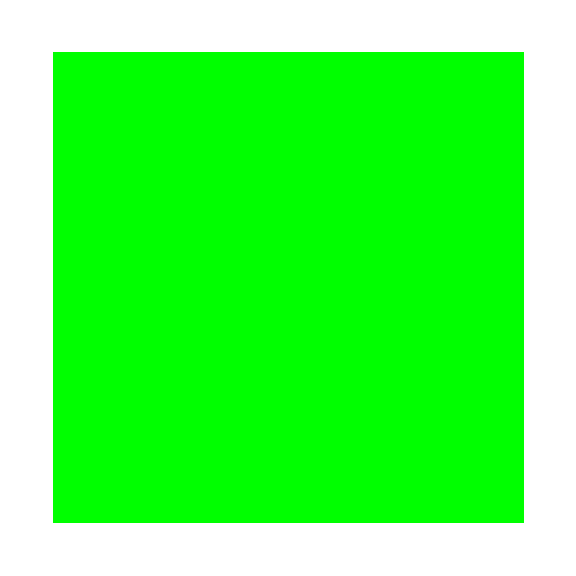

```mathematica
differences=MapThread[Not@*Equal,{CovMatrix50x30tabzSKA[[1]],Transpose[CovMatrix30x50tabzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixzSKA[[1]],Transpose[MultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

## COVARIANCE MATRIX + OCTUPOLE JOINT 70x50

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
CovMatrixOCT50Bx50FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrixOCT70Bx30FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-70B_30F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrixOCT50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrixOCT70Bx30FzSKA[[1,1,1]]
```

5.05678×10^-6

```mathematica
MultiSplitCovMatrixOCTzSKA = Table[
Join[ArrayFlatten[{{CovMatrixOCT50Bx50FzSKA[[i]], CovMatrixOCT50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrixOCT30x50tabzSKA[[i]], CovMatrixOCT70Bx30FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixOCTzSKA]
```

{19,648,648}

```mathematica
MultiSplitCovMatrixOCTzSKA[[All,325;;648,325;;648]]== CovMatrixOCT70Bx30FzSKA[[All]]
MultiSplitCovMatrixOCTzSKA[[All,1;;324,325;;648]]== CovMatrixOCT50x30tabzSKA[[All]]
MultiSplitCovMatrixOCTzSKA[[All,325;;648,1;;324]]== CovMatrixOCT30x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrixOCT50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrixOCT30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrixOCT50x30tabzSKA[[i]] ==CovMatrixOCT30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

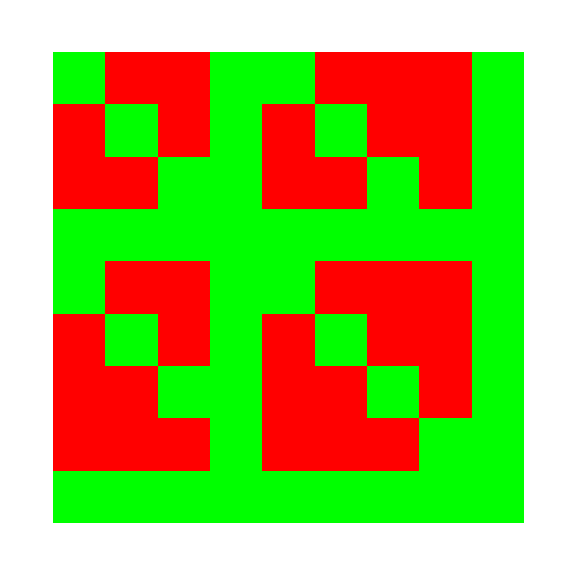

```mathematica
differences=MapThread[Not@*Equal,{CovMatrixOCT50x30tabzSKA[[1]],CovMatrixOCT30x50tabzSKA[[1]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrixOCT50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrixOCT30x50tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixOCTzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixOCTzSKA[[1]],Transpose[MultiSplitCovMatrixOCTzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixOCTzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixOCTzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

# EXPORT

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
Dimensions[MultiSplitCovMatrixOCTzSKA]
```

{19,576,576}

{19,648,648}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_all_50x70_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrixOCT_all_50x70_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixOCTzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
Exit[]
```